# FEM code for VDM

The implementation of VDM is relatively simple. The implementation is very similar to the standard FEM. 
The key functions include “EnergyDensity2Dspectral, EnergyDensity3Dspectral, OneElementMatrixVD2d, OneElementMatrixVD3d, OneElementMatrixVD2dOrder, and OneElementMatrixVD3dOrder”. These four functions calculate “positive”/”negative” energy density ϕ⁺/ϕ⁻, “positive”/”negative”  residual R⁺/R⁻, “positive”/”negative” material tensor D⁺/D⁻.  
These functions are not well organized. The code is not well commented.

## Eigenvalue decomposition and spectral decomposition of strain energy in 2D

```mathematica
h$t$pa=.;AbortReady[]:=Block[{},h$t$pa=.;h$t$pa="Alter file to abort MMA.txt";
If[FileExistsQ[h$t$pa],DeleteFile[h$t$pa]];
file=CreateFile[h$t$pa];
StartProcess[{"Notepad.exe",h$t$pa}];];
AbortCheck[]:=Block[{res},If[!ValueQ[h$t$pa],AbortReady[]];
If[FileExistsQ[h$t$pa],res=ReadList[h$t$pa,String,1];
If[Length[res]>0,h$t$pa=.;Abort[]]]]
```

```mathematica
Clear[Print0]
Print0[expr_]:=(SelectionMove[MessagesNotebook[],After,Cell];
NotebookWrite[MessagesNotebook[],Cell[BoxData["During evaluation of In["<>ToString@$Line<>"]"],"CellLabel"]];
NotebookWrite[MessagesNotebook[],Cell[BoxData[ToBoxes[expr]],"Print"]])
```

```mathematica
Round1[x_,n_:3]:=Block[{m},m=If[x==0.,0.,Round[Log10[Abs[x]]]];Round[x 10^(n-m)] 10.^(m-n)]
SetAttributes[Round1,Listable]
```

### Extract node force and

```mathematica
ExtractNodeForce[Rsp_,nodeList_,ndim_]:=Table[Normal[Rsp[[(nodeList-1)ndim+i]]],{i,ndim}]
ExtractNodeForce[Rsp_,nodeList_,ndim_,idim_]:=Normal[Rsp[[(nodeList-1)ndim+idim]]]
GaussPointToNodeValue[gpData_,ele_,node_,gpShapeN_]:=Block[{invN=Inverse[gpShapeNᵀ.gpShapeN].gpShapeNᵀ,dataE,dataN,nodeCount,ei},dataE=Table[invN.egp,{egp,gpData}];
dataN=Table[0.,{Length[node]}];
nodeCount=Table[0,{Length[node]}];
Do[ei=ele[[ii]];dataN[[ei]]+=dataE[[ii]];nodeCount[[ei]]+=1;,{ii,Length[ele]}];
dataN/nodeCount
]
GaussPointToNode=Compile[{{gpData,_Real,2},{ele,_Integer,2},{node,_Real,2},{gpShapeN,_Real,2}},Block[{invN=Inverse[gpShapeNᵀ.gpShapeN].gpShapeNᵀ,dataE,dataN,nodeCount,ei},dataE=Table[invN.egp,{egp,gpData}];
dataN=Table[0.,{Length[node]}];
nodeCount=Table[0,{Length[node]}];
Do[ei=ele[[ii]];dataN[[ei]]+=dataE[[ii]];nodeCount[[ei]]+=1;,{ii,Length[ele]}];
dataN/nodeCount
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
(*GaussPointToNode is almost 10 times faster than GaussPointToNodeValue*)
```

```mathematica
MeanGaussPointToNode=Compile[{{gpData,_Real,2},{ele,_Integer,2},{node,_Real,2}},Block[{dataE,dataN,nodeCount,ei},dataE=Table[Mean[egp],{egp,gpData}];
dataN=Table[0.,{Length[node]}];
nodeCount=Table[0,{Length[node]}];
Do[ei=ele[[ii]];dataN[[ei]]+=dataE[[ii]];nodeCount[[ei]]+=1;,{ii,Length[ele]}];
dataN/nodeCount
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
Eigensystem2=Compile[{{m,_Real,2}},Block[{em,el,ev,a$,b$,c$,em0},{a$,b$,c$}=Chop[{m[[1,1]],m[[1,2]],m[[2,2]]}];em=Sqrt[a$^2+4 b$^2-2 a$ c$+c$^2];
em0=If[em<10^-14,10^-14,em];el={0.5 (a$+c$-em0),0.5 (a$+c$+em0)};ev={a$-c$-em+10.^-30,2 b$} /Sqrt[10.^-60+4 b$^2+(a$-c$-em)^2];{el[[1]],el[[2]],ev[[1]],ev[[2]],-ev[[2]],ev[[1]]}]];
Eigensystem2v=Compile[{{m,_Real,1}(*m11,m12,m22*)},Block[{em,el,ev,a$,b$,c$,em0},{a$,b$,c$}=Chop[m];em=Sqrt[a$^2+4 b$^2-2 a$ c$+c$^2];
em0=If[em<10^-14,10^-14,em];el={0.5 (a$+c$-em0),0.5 (a$+c$+em0)};ev={a$-c$-em+10.^-30,2 b$} /Sqrt[10.^-60+4 b$^2+(a$-c$-em)^2];{el[[1]],el[[2]],ev[[1]],ev[[2]],-ev[[2]],ev[[1]]}]];
EnergyDensity2Dspectral=Compile[{{m22,_Real,1},{mat,_Real,1(*El,nu,type(0:plane stress, 1:plane strain)*)}},Block[{$l1 ,$l2,$v1,$v2,$v3,$v4,ϕ1,ϕ2,ϕv,c1,c2,ϕP=0.,ϕN=0.,RK10p=Table[0.,{10}](*{f000,f100,f010,f001,f200,f110,f101,f020,f011,f002},(εx,εxy,εy),{ϕ,ϕεx,ϕεxy,ϕεy,ϕεxεx,ϕεxεxy,ϕεxεy,ϕεxyεxy,ϕεxyεy,ϕεyεy}*),RK10n=Table[0.,{10}],RKtemp},{$l1 ,$l2,$v1,$v2,$v3,$v4}=Eigensystem2v[m22];
If[mat[[3]]==0.,{c1,c2}=mat[[1]]/(1-mat[[2]]^2){mat[[2]],1-mat[[2]]},{c1,c2}=mat[[1]]/(1-2mat[[2]])/(1+mat[[2]]){mat[[2]],1-2mat[[2]]}];
ϕv=c1 ($l1+$l2)^2/2;
ϕ1=c2 $l1^2/2;
ϕ2=c2 $l2^2/2;
RKtemp=c1{($l1+$l2)^2/2,($l1+$l2)*($v1^2+$v3^2),2*($l1+$l2)*($v1*$v2+$v3*$v4),($l1+$l2)*($v2^2+$v4^2),($v1^2+$v3^2)^2,2*($v1^2+$v3^2)*($v1*$v2+$v3*$v4),($v1^2+$v3^2)*($v2^2+$v4^2),4*($v1*$v2+$v3*$v4)^2,2*($v1*$v2+$v3*$v4)*($v2^2+$v4^2),($v2^2+$v4^2)^2};
If[$l1+$l2>0.,RK10p+=RKtemp;,RK10n+=RKtemp];
RKtemp=c2{$l1^2/2,$l1*$v1^2,2*$l1*$v1*$v2,$l1*$v2^2,$v1^4+(2*$l1*$v1^2*$v3^2)/($l1-$l2),2*$v1^3*$v2+(2*$l1*$v1*$v3*($v2*$v3+$v1*$v4))/($l1-$l2),$v1*$v2*($v1*$v2+(2*$l1*$v3*$v4)/($l1-$l2)),(-4*$l2*$v1^2*$v2^2+2*$l1*($v2^2*$v3^2+2*$v1*$v2*$v3*$v4+$v1^2*(2*$v2^2+$v4^2)))/($l1-$l2),(-2*$l2*$v1*$v2^3+2*$l1*$v2*($v2*$v3*$v4+$v1*($v2^2+$v4^2)))/($l1-$l2),$v2^4+(2*$l1*$v2^2*$v4^2)/($l1-$l2)};
If[$l1>0.,RK10p+=RKtemp;,RK10n+=RKtemp];
RKtemp=c2{$l2^2/2,$l2*$v3^2,2*$l2*$v3*$v4,$l2*$v4^2,(2*$l2*$v1^2*$v3^2)/(-$l1+$l2)+$v3^4,2*$v3^3*$v4+(2*$l2*$v1*$v3*($v2*$v3+$v1*$v4))/(-$l1+$l2),$v3*$v4*((2*$l2*$v1*$v2)/(-$l1+$l2)+$v3*$v4),(4*$l1*$v3^2*$v4^2-2*$l2*($v2^2*$v3^2+2*$v1*$v2*$v3*$v4+($v1^2+2*$v3^2)*$v4^2))/($l1-$l2),(-2*$l1*$v3*$v4^3+2*$l2*$v4*($v2^2*$v3+$v1*$v2*$v4+$v3*$v4^2))/(-$l1+$l2),(2*$l2*$v2^2*$v4^2)/(-$l1+$l2)+$v4^4};
If[$l2>0.,RK10p+=RKtemp;,RK10n+=RKtemp];

{RK10p,RK10n}
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];

EnergyDensity2D=Compile[{{m22,_Real,1},{mat,_Real,1(*El,nu,type(0:plane stress, 1:plane strain)*)}},Block[{c1,c2,ε1,ε2,ε3,RK10p=Table[0.,{10}](*{f000,f100,f010,f001,f200,f110,f101,f020,f011,f002},(εx,εxy,εy),{ϕ,ϕεx,ϕεxy,ϕεy,ϕεxεx,ϕεxεxy,ϕεxεy,ϕεxyεxy,ϕεxyεy,ϕεyεy}*),RK10n=Table[0.,{10}],El=mat[[1]],v=mat[[2]],c3},
If[mat[[3]]==0.,c3=mat[[1]]/(1-mat[[2]]^2),c3=mat[[1]]/(1-2mat[[2]])/(1+mat[[2]])];
{ε1,ε2,ε3}=m22;
If[mat[[3]]==0,RK10p=c3{1/2 (ε1^2-2 (-1+v) ε2^2+2 v ε1 ε3+ε3^2),ε1+v ε3,-2 (-1+v) ε2,v ε1+ε3,1,0,v,2-2 v,0,1},RK10p=c3{1/2 (-((-1+v) ε1^2)+(2-4 v) ε2^2+2 v ε1 ε3-(-1+v) ε3^2),ε1-v ε1+v ε3,2 (1-2 v) ε2,v (ε1-ε3)+ε3,1-v,0,v,2-4 v,0,1-v}];
{RK10p,RK10n}
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
EnergyDensity3Dvoldev=Compile[{{m22,_Real,1},{mat,_Real,1(*El,nu,type(0:plane stress, 1:plane strain)*)}},Block[{c1,c2,ε1,ε2,ε3,ε4,ε5,ε6,RK10p=Table[0.,{28}](*{f000,f100,f010,f001,f200,f110,f101,f020,f011,f002},(εx,εxy,εy),{ϕ,ϕεx,ϕεxy,ϕεy,ϕεxεx,ϕεxεxy,ϕεxεy,ϕεxyεxy,ϕεxyεy,ϕεyεy}*),RK10n=Table[0.,{28}],RKtemp},
{c1,c2}={mat[[1]]/3/(1-2mat[[2]]),mat[[1]]/(1+mat[[2]])};
{ε1,ε2,ε3,ε4,ε5,ε6}=m22;

RK10n=c1{1/6 (ε1+ε4+ε6)^2,1/3 (ε1+ε4+ε6),0,0,1/3 (ε1+ε4+ε6),0,1/3 (ε1+ε4+ε6),1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3};
RK10p=c2{1/3 (ε1^2+3 ε2^2+3 ε3^2+ε4^2+3 ε5^2-ε4 ε6+ε6^2-ε1 (ε4+ε6)),1/3 (2 ε1-ε4-ε6),2 ε2,2 ε3,1/3 (-ε1+2 ε4-ε6),2 ε5,1/3 (-ε1-ε4+2 ε6),2/3,0,0,-1/3,0,-1/3,2,0,0,0,0,2,0,0,0,2/3,0,-1/3,2,0,2/3};
If[(ε1+ε4+ε6)>0.,RK10p+=RK10n;RK10n[[All]]=0.];
{RK10p,RK10n}
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
EnergyDensity3D=Compile[{{m22,_Real,1},{mat,_Real,1(*El,nu,type(0:plane stress, 1:plane strain)*)}},Block[{c1,c2,ε1,ε2,ε3,ε4,ε5,ε6,RK10p=Table[0.,{28}](*{f000,f100,f010,f001,f200,f110,f101,f020,f011,f002},(εx,εxy,εy),{ϕ,ϕεx,ϕεxy,ϕεy,ϕεxεx,ϕεxεxy,ϕεxεy,ϕεxyεxy,ϕεxyεy,ϕεyεy}*),RK10n=Table[0.,{28}],RKtemp,El=mat[[1]],v=mat[[2]]},
{c1,c2}={mat[[1]]/3/(1-2mat[[2]]),mat[[1]]/(1+mat[[2]])};
c1=El/((1-2 v) (1+v));
{ε1,ε2,ε3,ε4,ε5,ε6}=m22;

RK10n=c1{0.,ε1-v ε1+v (ε4+ε6),2 (1-2 v) ε2,2 (1-2 v) ε3,ε4+v (ε1-ε4+ε6),2 (1-2 v) ε5,v (ε1+ε4-ε6)+ε6,1-v,0,0,v,0,v,2-4 v,0,0,0,0,2-4 v,0,0,0,1-v,0,v,2-4 v,0,1-v};
{RK10p,RK10n}
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
```

### EnergyDensity2DspectralDecomposition

```mathematica
Eigensystem3Dv=Compile[{{m$,_Real,1}},Block[{a$,b$,c$,d$,e$,f$,dn$,dd$,cc$,bb$,d1$,d$1,C$,r$$0,nx$=1,x1$=0.,x2$=0.,x3$=0.,v1$,v2$,v3$,tol$=10.^-24,ndim=Length[m$],maxx=0.,dx,dy,ixyz,xyz,v123,told=10.^-14,tol2=0.,mmax=0.},tol2=told^2;mmax=Max[Max[Abs[m$[[1]]],Abs[m$[[2]]]],Max[Abs[m$[[3]]],Abs[m$[[4]]]],Max[Abs[m$[[5]]],Abs[m$[[6]]]]];
mmax=1/(mmax+tol2);{a$,b$,c$,d$,e$,f$}=Chop[{m$[[1]]mmax,m$[[2]]mmax,m$[[3]]mmax,m$[[4]]mmax,m$[[5]]mmax,m$[[6]]mmax}];
dn$=b$ b$+c$ c$+e$ e$;(*p1*){v1$,v2$,v3$}={{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}};
If[dn$<tol2,{x1$,x2$,x3$}={a$,d$,f$};
nx$=1,dd$=(a$+d$+f$)/3.;(*q*)(*cc$=a$ a$+d$ d$+f$ f$-3 dd$ dd$+2 dn$;There is a bug. Remember there is (a$-d$)^2+(a$-f$)^2+(d$-f$)^2==(3a$ a$+3d$ d$+3f$ f$-(a$+d$+f$)^2)*)
cc$=1/3((a$-d$)^2+(a$-f$)^2+(d$-f$)^2(*3a$ a$+3d$ d$+3f$ f$-(a$+d$+f$)^2*)) +2 dn$;
(*p2*)bb$=Sqrt[cc$/6];(*p*)d1$=a$ d$ f$+2 b$ e$ c$-a$ e$ e$-d$ c$ c$-f$ b$ b$;(*detA*)d$1=0.5 (d1$+dd$ dn$+2 dd$^3-dd$ (a$ d$+a$ f$+d$ f$))/bb$^3;
If[Abs[d$1]≥1.,If[d$1≤-1.,nx$=2;{x1$,x3$}={dd$+bb$,dd$-2 bb$};
x2$=x1$];
If[d$1≥1.,nx$=2;{x1$,x3$}={dd$-bb$,dd$+2 bb$};
x2$=x1$];,C$=ArcCos[d$1]/3.;nx$=3;
{x1$,x2$}={dd$+2 bb$ Cos[C$],dd$+2 bb$ Cos[C$+2. π/3]};
x3$=3 dd$-x1$-x2$;];];
If[nx$==2,v3$={-e$^2+(d$-x3$) (f$-x3$),c$ e$+b$ (-f$+x3$),b$ e$+c$ (-d$+x3$)};
r$$0=Sqrt[v3$.v3$];
If[r$$0<tol2,v3$={0.,0.,1.},v3$*=1./r$$0];
v2$=v3$+RandomReal[1.,3];
v2$-=(v3$.v2$) v3$;
v2$*=1./Sqrt[v2$.v2$];
v1$=Cross[v2$,v3$];];
If[nx$==3,v1$={-e$^2+(d$-x1$) (f$-x1$),c$ e$+b$ (-f$+x1$),b$ e$+c$ (-d$+x1$)};
r$$0=Sqrt[v1$.v1$];
If[r$$0<tol2,v1$={1.,0.,0.},v1$*=1./r$$0];
v2$={-e$^2+(d$-x2$) (f$-x2$),c$ e$+b$ (-f$+x2$),b$ e$+c$ (-d$+x2$)};
r$$0=Sqrt[v2$.v2$];
If[r$$0<tol2,v2$={0.,1.,0.},v2$*=1./r$$0];
v2$*=1./Sqrt[v2$.v2$];v3$=Cross[v1$,v2$]];
(*Make the eigenvalue distinct*)
xyz={x1$,x2$,x3$};
v123={v1$,v2$,v3$};
ixyz=Ordering[xyz];
xyz=xyz[[ixyz]];
(*v123=v123[[ixyz]];*)
x1$=xyz[[1]];x2$=xyz[[2]];x3$=xyz[[3]];
v1$=v123[[ixyz[[1]]]];
v2$=v123[[ixyz[[2]]]];
v3$=v123[[ixyz[[3]]]];

maxx=1./(told+Max[Abs[x1$],Abs[x3$]]);
dx=(x2$-x1$)maxx;
dy=(x3$-x2$)maxx;
(*told=told/maxx;*)
If[dx<told && dy>told,x1$-=told];
If[dy<told && dx>told,x3$+=told];
If[dx<told && dy<told,x1$-=told;x3$+=told];
{x1$/mmax,x2$/mmax,x3$/mmax,v1$[[1]],v1$[[2]],v1$[[3]],v2$[[1]],v2$[[2]],v2$[[3]],v3$[[1]],v3$[[2]],v3$[[3]]}]];
```

```mathematica
(*return RK10p=(ϕ⁺,σ⁺,dσ⁺/dε), RK10n=(ϕ⁻,σ⁻,dσ⁻/dε)*)
EnergyDensity3Dspectral=Compile[{{m22,_Real,1},{mat,_Real,1(*El,nu,type(0:plane stress, 1:plane strain)*)}},Block[{$l1 ,$l2,$l3,$v1,$v2,$v3,$v4,$v5,$v6,$v7,$v8,$v9,ϕ1,ϕ2,ϕ3,ϕv,c1,c2,ϕP=0.,ϕN=0.,RK10p=Table[0.,{28}](*{f000,f100,f010,f001,f200,f110,f101,f020,f011,f002},(εx,εxy,εy),{ϕ,ϕεx,ϕεxy,ϕεy,ϕεxεx,ϕεxεxy,ϕεxεy,ϕεxyεxy,ϕεxyεy,ϕεyεy}*),RK10n=Table[0.,{28}],RKtemp},{$l1 ,$l2,$l3,$v1,$v2,$v3,$v4,$v5,$v6,$v7,$v8,$v9}=Eigensystem3Dv[m22];
(*If[mat[[3]]==0.,{c1,c2}=mat[[1]]/(1-mat[[2]]^2){mat[[2]],1-mat[[2]]},*){c1,c2}=mat[[1]]/(1-2mat[[2]])/(1+mat[[2]]){mat[[2]],1-2mat[[2]]};
ϕv=c1 ($l1+$l2+$l3)^2/2;
ϕ1=c2 $l1^2/2;
ϕ2=c2 $l2^2/2;
ϕ3=c2 $l3^2/2;
RKtemp=c1{($l1+$l2+$l3)^2/2,($l1+$l2+$l3)*($v1^2+$v4^2+$v7^2),2*($l1+$l2+$l3)*($v1*$v2+$v4*$v5+$v7*$v8),2*($l1+$l2+$l3)*($v1*$v3+$v4*$v6+$v7*$v9),($l1+$l2+$l3)*($v2^2+$v5^2+$v8^2),2*($l1+$l2+$l3)*($v2*$v3+$v5*$v6+$v8*$v9),($l1+$l2+$l3)*($v3^2+$v6^2+$v9^2),($v1^2+$v4^2+$v7^2)^2,2*($v1^2+$v4^2+$v7^2)*($v1*$v2+$v4*$v5+$v7*$v8),2*($v1^2+$v4^2+$v7^2)*($v1*$v3+$v4*$v6+$v7*$v9),($v1^2+$v4^2+$v7^2)*($v2^2+$v5^2+$v8^2),2*($v1^2+$v4^2+$v7^2)*($v2*$v3+$v5*$v6+$v8*$v9),($v1^2+$v4^2+$v7^2)*($v3^2+$v6^2+$v9^2),4*($v1*$v2+$v4*$v5+$v7*$v8)^2,4*($v1*$v2+$v4*$v5+$v7*$v8)*($v1*$v3+$v4*$v6+$v7*$v9),2*($v1*$v2+$v4*$v5+$v7*$v8)*($v2^2+$v5^2+$v8^2),4*($v1*$v2+$v4*$v5+$v7*$v8)*($v2*$v3+$v5*$v6+$v8*$v9),2*($v1*$v2+$v4*$v5+$v7*$v8)*($v3^2+$v6^2+$v9^2),4*($v1*$v3+$v4*$v6+$v7*$v9)^2,2*($v2^2+$v5^2+$v8^2)*($v1*$v3+$v4*$v6+$v7*$v9),4*($v1*$v3+$v4*$v6+$v7*$v9)*($v2*$v3+$v5*$v6+$v8*$v9),2*($v1*$v3+$v4*$v6+$v7*$v9)*($v3^2+$v6^2+$v9^2),($v2^2+$v5^2+$v8^2)^2,2*($v2^2+$v5^2+$v8^2)*($v2*$v3+$v5*$v6+$v8*$v9),($v2^2+$v5^2+$v8^2)*($v3^2+$v6^2+$v9^2),4*($v2*$v3+$v5*$v6+$v8*$v9)^2,2*($v2*$v3+$v5*$v6+$v8*$v9)*($v3^2+$v6^2+$v9^2),($v3^2+$v6^2+$v9^2)^2};
If[$l1+$l2+$l3>0.,RK10p+=RKtemp;,RK10n+=RKtemp];
RKtemp=c2{$l1^2/2,$l1*$v1^2,2*$l1*$v1*$v2,2*$l1*$v1*$v3,$l1*$v2^2,2*$l1*$v2*$v3,$l1*$v3^2,$v1^4+2*$l1*$v1^2*($v4^2/($l1-$l2)+$v7^2/($l1-$l3)),2*$v1^3*$v2+2*$l1*$v1*($v2*($v4^2/($l1-$l2)+$v7^2/($l1-$l3))+$v1*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))),2*$v1^3*$v3+2*$l1*$v1*($v3*($v4^2/($l1-$l2)+$v7^2/($l1-$l3))+$v1*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3))),$v1*$v2*($v1*$v2+2*$l1*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))),2*$v1*($v1*$v2*$v3+$l1*($v3*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))+$v2*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3)))),$v1*$v3*($v1*$v3+2*$l1*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3))),2*($l1*$v2^2*($v4^2/($l1-$l2)+$v7^2/($l1-$l3))+2*$l1*$v1*$v2*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))+$v1^2*(2*$v2^2+$l1*($v5^2/($l1-$l2)+$v8^2/($l1-$l3)))),4*$v1^2*$v2*$v3+2*$l1*$v2*($v3*($v4^2/($l1-$l2)+$v7^2/($l1-$l3))+$v1*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3)))+2*$l1*$v1*($v3*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))+$v1*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3))),2*$v2*($l1*$v2*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))+$v1*($v2^2+$l1*($v5^2/($l1-$l2)+$v8^2/($l1-$l3)))),2*$l1*$v2*($v3*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))+$v2*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3)))+2*$v1*(2*$v2^2*$v3+$l1*$v3*($v5^2/($l1-$l2)+$v8^2/($l1-$l3))+$l1*$v2*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3))),2*$v3*($l1*$v2*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3))+$v1*($v2*$v3+$l1*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3)))),2*($l1*$v3^2*($v4^2/($l1-$l2)+$v7^2/($l1-$l3))+2*$l1*$v1*$v3*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3))+$v1^2*(2*$v3^2+$l1*($v6^2/($l1-$l2)+$v9^2/($l1-$l3)))),2*$v2*($l1*$v3*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))+$v1*($v2*$v3+$l1*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3)))),2*$l1*$v3*($v3*(($v4*$v5)/($l1-$l2)+($v7*$v8)/($l1-$l3))+$v2*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3)))+2*$v1*($l1*$v3*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3))+$v2*(2*$v3^2+$l1*($v6^2/($l1-$l2)+$v9^2/($l1-$l3)))),2*$v3*($l1*$v3*(($v4*$v6)/($l1-$l2)+($v7*$v9)/($l1-$l3))+$v1*($v3^2+$l1*($v6^2/($l1-$l2)+$v9^2/($l1-$l3)))),$v2^4+2*$l1*$v2^2*($v5^2/($l1-$l2)+$v8^2/($l1-$l3)),2*$v2^3*$v3+2*$l1*$v2*($v3*($v5^2/($l1-$l2)+$v8^2/($l1-$l3))+$v2*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3))),$v2*$v3*($v2*$v3+2*$l1*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3))),2*($l1*$v3^2*($v5^2/($l1-$l2)+$v8^2/($l1-$l3))+2*$l1*$v2*$v3*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3))+$v2^2*(2*$v3^2+$l1*($v6^2/($l1-$l2)+$v9^2/($l1-$l3)))),2*$v3*($l1*$v3*(($v5*$v6)/($l1-$l2)+($v8*$v9)/($l1-$l3))+$v2*($v3^2+$l1*($v6^2/($l1-$l2)+$v9^2/($l1-$l3)))),$v3^4+2*$l1*$v3^2*($v6^2/($l1-$l2)+$v9^2/($l1-$l3))};
If[$l1>0.,RK10p+=RKtemp;,RK10n+=RKtemp];
RKtemp=c2{$l2^2/2,$l2*$v4^2,2*$l2*$v4*$v5,2*$l2*$v4*$v6,$l2*$v5^2,2*$l2*$v5*$v6,$l2*$v6^2,$v4^4+2*$l2*$v4^2*($v1^2/(-$l1+$l2)+$v7^2/($l2-$l3)),2*$v4^3*$v5+2*$l2*$v4*(($v1*$v2*$v4)/(-$l1+$l2)+($v1^2*$v5)/(-$l1+$l2)+($v7*($v5*$v7+$v4*$v8))/($l2-$l3)),2*$v4^3*$v6+2*$l2*$v4*(($v1*$v3*$v4)/(-$l1+$l2)+($v1^2*$v6)/(-$l1+$l2)+($v7*($v6*$v7+$v4*$v9))/($l2-$l3)),$v4*$v5*($v4*$v5+2*$l2*(($v1*$v2)/(-$l1+$l2)+($v7*$v8)/($l2-$l3))),2*$v4*($v4*$v5*$v6+$l2*(-(($v1*($v3*$v5+$v2*$v6))/($l1-$l2))+($v7*($v6*$v8+$v5*$v9))/($l2-$l3))),$v4*$v6*($v4*$v6+2*$l2*(($v1*$v3)/(-$l1+$l2)+($v7*$v9)/($l2-$l3))),4*$v4^2*$v5^2+(2*$l2*($l3*($v2*$v4+$v1*$v5)^2+$l1*($v5*$v7+$v4*$v8)^2-$l2*($v2^2*$v4^2+2*$v1*$v2*$v4*$v5+$v1^2*$v5^2+($v5*$v7+$v4*$v8)^2)))/(($l1-$l2)*($l2-$l3)),4*$v4^2*$v5*$v6+2*$l2*$v5*(($v1*$v3*$v4)/(-$l1+$l2)+($v1^2*$v6)/(-$l1+$l2)+($v7*($v6*$v7+$v4*$v9))/($l2-$l3))+2*$l2*$v4*(-(($v2*($v3*$v4+$v1*$v6))/($l1-$l2))+($v8*($v6*$v7+$v4*$v9))/($l2-$l3)),2*$v5*($v4*$v5^2+$l2*(($v2^2*$v4)/(-$l1+$l2)+($v1*$v2*$v5)/(-$l1+$l2)+($v8*($v5*$v7+$v4*$v8))/($l2-$l3))),4*$v4*$v5^2*$v6+2*$l2*$v5*(-(($v1*($v3*$v5+$v2*$v6))/($l1-$l2))+($v7*($v6*$v8+$v5*$v9))/($l2-$l3))+2*$l2*$v4*(($v2*$v3*$v5)/(-$l1+$l2)+($v2^2*$v6)/(-$l1+$l2)+($v8*($v6*$v8+$v5*$v9))/($l2-$l3)),2*$v6*($v4*$v5*$v6+$l2*$v5*(($v1*$v3)/(-$l1+$l2)+($v7*$v9)/($l2-$l3))+$l2*$v4*(($v2*$v3)/(-$l1+$l2)+($v8*$v9)/($l2-$l3))),4*$v4^2*$v6^2+(2*$l2*($l3*($v3*$v4+$v1*$v6)^2+$l1*($v6*$v7+$v4*$v9)^2-$l2*($v3^2*$v4^2+2*$v1*$v3*$v4*$v6+$v1^2*$v6^2+($v6*$v7+$v4*$v9)^2)))/(($l1-$l2)*($l2-$l3)),2*$v5*($v4*$v5*$v6+$l2*(-(($v2*($v3*$v4+$v1*$v6))/($l1-$l2))+($v8*($v6*$v7+$v4*$v9))/($l2-$l3))),4*$v4*$v5*$v6^2+2*$l2*$v6*(-(($v1*($v3*$v5+$v2*$v6))/($l1-$l2))+($v7*($v6*$v8+$v5*$v9))/($l2-$l3))+2*$l2*$v4*(($v3^2*$v5)/(-$l1+$l2)+($v2*$v3*$v6)/(-$l1+$l2)+($v9*($v6*$v8+$v5*$v9))/($l2-$l3)),2*$v6*($v4*$v6^2+$l2*(($v3^2*$v4)/(-$l1+$l2)+($v1*$v3*$v6)/(-$l1+$l2)+($v9*($v6*$v7+$v4*$v9))/($l2-$l3))),$v5^4+2*$l2*$v5^2*($v2^2/(-$l1+$l2)+$v8^2/($l2-$l3)),2*$v5^3*$v6+2*$l2*$v5*(($v2*$v3*$v5)/(-$l1+$l2)+($v2^2*$v6)/(-$l1+$l2)+($v8*($v6*$v8+$v5*$v9))/($l2-$l3)),$v5*$v6*($v5*$v6+2*$l2*(($v2*$v3)/(-$l1+$l2)+($v8*$v9)/($l2-$l3))),4*$v5^2*$v6^2+(2*$l2*($l3*($v3*$v5+$v2*$v6)^2+$l1*($v6*$v8+$v5*$v9)^2-$l2*($v3^2*$v5^2+2*$v2*$v3*$v5*$v6+$v2^2*$v6^2+($v6*$v8+$v5*$v9)^2)))/(($l1-$l2)*($l2-$l3)),2*$v6*($v5*$v6^2+$l2*(($v3^2*$v5)/(-$l1+$l2)+($v2*$v3*$v6)/(-$l1+$l2)+($v9*($v6*$v8+$v5*$v9))/($l2-$l3))),$v6^4+2*$l2*$v6^2*($v3^2/(-$l1+$l2)+$v9^2/($l2-$l3))};
If[$l2>0.,RK10p+=RKtemp;,RK10n+=RKtemp];

RKtemp=c2 {$l3^2/2,$l3*$v7^2,2*$l3*$v7*$v8,2*$l3*$v7*$v9,$l3*$v8^2,2*$l3*$v8*$v9,$l3*$v9^2,2*$l3*($v1^2/(-$l1+$l3)+$v4^2/(-$l2+$l3))*$v7^2+$v7^4,2*$v7^3*$v8+2*$l3*$v7*(($v1*$v2*$v7)/(-$l1+$l3)+($v1^2*$v8)/(-$l1+$l3)-($v4*($v5*$v7+$v4*$v8))/($l2-$l3)),2*$v7^3*$v9+2*$l3*$v7*(($v1*$v3*$v7)/(-$l1+$l3)+($v1^2*$v9)/(-$l1+$l3)-($v4*($v6*$v7+$v4*$v9))/($l2-$l3)),$v7*$v8*(2*$l3*(($v1*$v2)/(-$l1+$l3)+($v4*$v5)/(-$l2+$l3))+$v7*$v8),2*$v7*($v7*$v8*$v9+$l3*(-(($v1*($v3*$v8+$v2*$v9))/($l1-$l3))-($v4*($v6*$v8+$v5*$v9))/($l2-$l3))),$v7*$v9*(2*$l3*(($v1*$v3)/(-$l1+$l3)+($v4*$v6)/(-$l2+$l3))+$v7*$v9),4*$v7^2*$v8^2+2*$l3*(($v2^2*$v7^2)/(-$l1+$l3)+($v5^2*$v7^2)/(-$l2+$l3)+(2*$v1*$v2*$v7*$v8)/(-$l1+$l3)+(2*$v4*$v5*$v7*$v8)/(-$l2+$l3)+($v1^2/(-$l1+$l3)+$v4^2/(-$l2+$l3))*$v8^2),4*$v7^2*$v8*$v9+2*$l3*$v8*(($v1*$v3*$v7)/(-$l1+$l3)+($v1^2*$v9)/(-$l1+$l3)-($v4*($v6*$v7+$v4*$v9))/($l2-$l3))+2*$l3*$v7*(-(($v2*($v3*$v7+$v1*$v9))/($l1-$l3))-($v5*($v6*$v7+$v4*$v9))/($l2-$l3)),2*$v8*($v7*$v8^2+$l3*(($v2^2*$v7)/(-$l1+$l3)+($v1*$v2*$v8)/(-$l1+$l3)-($v5*($v5*$v7+$v4*$v8))/($l2-$l3))),4*$v7*$v8^2*$v9+2*$l3*$v8*(-(($v1*($v3*$v8+$v2*$v9))/($l1-$l3))-($v4*($v6*$v8+$v5*$v9))/($l2-$l3))+2*$l3*$v7*(($v2*$v3*$v8)/(-$l1+$l3)+($v2^2*$v9)/(-$l1+$l3)-($v5*($v6*$v8+$v5*$v9))/($l2-$l3)),2*$v9*($l3*(($v2*$v3)/(-$l1+$l3)+($v5*$v6)/(-$l2+$l3))*$v7+$l3*(($v1*$v3)/(-$l1+$l3)+($v4*$v6)/(-$l2+$l3))*$v8+$v7*$v8*$v9),4*$v7^2*$v9^2+2*$l3*(($v3^2*$v7^2)/(-$l1+$l3)+($v6^2*$v7^2)/(-$l2+$l3)+(2*$v1*$v3*$v7*$v9)/(-$l1+$l3)+(2*$v4*$v6*$v7*$v9)/(-$l2+$l3)+($v1^2/(-$l1+$l3)+$v4^2/(-$l2+$l3))*$v9^2),2*$v8*($v7*$v8*$v9+$l3*(-(($v2*($v3*$v7+$v1*$v9))/($l1-$l3))-($v5*($v6*$v7+$v4*$v9))/($l2-$l3))),4*$v7*$v8*$v9^2+2*$l3*$v9*(-(($v1*($v3*$v8+$v2*$v9))/($l1-$l3))-($v4*($v6*$v8+$v5*$v9))/($l2-$l3))+2*$l3*$v7*(($v3^2*$v8)/(-$l1+$l3)+($v2*$v3*$v9)/(-$l1+$l3)-($v6*($v6*$v8+$v5*$v9))/($l2-$l3)),2*$v9*($v7*$v9^2+$l3*(($v3^2*$v7)/(-$l1+$l3)+($v1*$v3*$v9)/(-$l1+$l3)-($v6*($v6*$v7+$v4*$v9))/($l2-$l3))),2*$l3*($v2^2/(-$l1+$l3)+$v5^2/(-$l2+$l3))*$v8^2+$v8^4,2*$v8^3*$v9+2*$l3*$v8*(($v2*$v3*$v8)/(-$l1+$l3)+($v2^2*$v9)/(-$l1+$l3)-($v5*($v6*$v8+$v5*$v9))/($l2-$l3)),$v8*$v9*(2*$l3*(($v2*$v3)/(-$l1+$l3)+($v5*$v6)/(-$l2+$l3))+$v8*$v9),4*$v8^2*$v9^2+2*$l3*(($v3^2*$v8^2)/(-$l1+$l3)+($v6^2*$v8^2)/(-$l2+$l3)+(2*$v2*$v3*$v8*$v9)/(-$l1+$l3)+(2*$v5*$v6*$v8*$v9)/(-$l2+$l3)+($v2^2/(-$l1+$l3)+$v5^2/(-$l2+$l3))*$v9^2),2*$v9*($v8*$v9^2+$l3*(($v3^2*$v8)/(-$l1+$l3)+($v2*$v3*$v9)/(-$l1+$l3)-($v6*($v6*$v8+$v5*$v9))/($l2-$l3))),2*$l3*($v3^2/(-$l1+$l3)+$v6^2/(-$l2+$l3))*$v9^2+$v9^4};
If[$l3>0.,RK10p+=RKtemp;,RK10n+=RKtemp];

{RK10p,RK10n}
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
```

## Conventional code for FEM

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"MeshIntegrationPoints.nb"];
NotebookEvaluate[NotebookDirectory[]<>"NOM_tools v0.nb"];
```

```mathematica
Area23=Compile[{{m,_Real,2}},Block[{nr=Length[m],nc=Length[m[[1]]],im},im=0.;
If[nc==2&&nr==1,Return[Sqrt[m[[1,1]]^2+m[[1,2]]^2]]];(*Length of line in 2D*)
If[nc==2&&nr==2,Return[Abs[-m[[1,2]] m[[2,1]]+m[[1,1]] m[[2,2]]]]];(*Area in 2D*)
If[nc==3&&nr==1,Return[Sqrt[m[[1,1]]^2+m[[1,2]]^2+m[[1,3]]^2]]];(*Length of line in 3D*)
If[nc==3&&nr==2,Return[Sqrt[(-m[[1,2]] m[[2,1]]+m[[1,1]] m[[2,2]])^2+(m[[1,3]] m[[2,1]]-m[[1,1]] m[[2,3]])^2+(-m[[1,3]] m[[2,2]]+m[[1,2]] m[[2,3]])^2]]];(*(*Area in 3D*)*)
If[nc==3&&nr==3,Return[Abs[-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]]]]];(*Volume in 3D*)
im]];
```

```mathematica
Otimes=Compile[{{a,_Real,1},{b,_Real,1}},Block[{res=Table[0.,{Length[a]},{Length[b]}]},Do[res[[i,j]]=a[[i]] b[[j]],{i,Length[a]},{j,Length[b]}];res]];
```

```mathematica
(*return the (pseudo-)inverse of low order matrix, 2d, 3d, the row≤ column,
ndim=2;nr=2;m=RandomReal[1,{nr,ndim}];Inverse23[m]//AbsoluteTiming
Inverse[m]//AbsoluteTiming
m.Inverse23[m]
*)
```

```mathematica
Inverse23=Compile[{{m,_Real,2}},Block[{nr=Length[m],nc=Length[m[[1]]],im},im=Table[0.,{nc},{nr}];
(*If[nr>3 || nc>nr,Return[im]];*)
If[nc==2&&nr==1,Return[{{m[[1,1]]/(m[[1,1]]^2+m[[1,2]]^2)},{m[[1,2]]/(m[[1,1]]^2+m[[1,2]]^2)}}]];
If[nc==2&&nr==2,Return[{{m[[2,2]]/(-m[[1,2]] m[[2,1]]+m[[1,1]] m[[2,2]]),-(m[[1,2]]/(-m[[1,2]] m[[2,1]]+m[[1,1]] m[[2,2]]))},{-(m[[2,1]]/(-m[[1,2]] m[[2,1]]+m[[1,1]] m[[2,2]])),m[[1,1]]/(-m[[1,2]] m[[2,1]]+m[[1,1]] m[[2,2]])}}]];
If[nc==3&&nr==1,Return[{{m[[1,1]]/(m[[1,1]]^2+m[[1,2]]^2+m[[1,3]]^2)},{m[[1,2]]/(m[[1,1]]^2+m[[1,2]]^2+m[[1,3]]^2)},{m[[1,3]]/(m[[1,1]]^2+m[[1,2]]^2+m[[1,3]]^2)}}]];
If[nc==3&&nr==2,Return[{{(-m[[1,2]] m[[2,1]] m[[2,2]]-m[[1,3]] m[[2,1]] m[[2,3]]+m[[1,1]] (m[[2,2]]^2+m[[2,3]]^2))/(m[[1,3]]^2 (m[[2,1]]^2+m[[2,2]]^2)-2 m[[1,1]] m[[1,3]] m[[2,1]] m[[2,3]]-2 m[[1,2]] m[[2,2]] (m[[1,1]] m[[2,1]]+m[[1,3]] m[[2,3]])+m[[1,2]]^2 (m[[2,1]]^2+m[[2,3]]^2)+m[[1,1]]^2 (m[[2,2]]^2+m[[2,3]]^2)),(m[[1,2]]^2 m[[2,1]]-m[[1,1]] m[[1,2]] m[[2,2]]+m[[1,3]] (m[[1,3]] m[[2,1]]-m[[1,1]] m[[2,3]]))/(m[[1,3]]^2 (m[[2,1]]^2+m[[2,2]]^2)-2 m[[1,1]] m[[1,3]] m[[2,1]] m[[2,3]]-2 m[[1,2]] m[[2,2]] (m[[1,1]] m[[2,1]]+m[[1,3]] m[[2,3]])+m[[1,2]]^2 (m[[2,1]]^2+m[[2,3]]^2)+m[[1,1]]^2 (m[[2,2]]^2+m[[2,3]]^2))},{(-m[[2,2]] (m[[1,1]] m[[2,1]]+m[[1,3]] m[[2,3]])+m[[1,2]] (m[[2,1]]^2+m[[2,3]]^2))/(m[[1,3]]^2 (m[[2,1]]^2+m[[2,2]]^2)-2 m[[1,1]] m[[1,3]] m[[2,1]] m[[2,3]]-2 m[[1,2]] m[[2,2]] (m[[1,1]] m[[2,1]]+m[[1,3]] m[[2,3]])+m[[1,2]]^2 (m[[2,1]]^2+m[[2,3]]^2)+m[[1,1]]^2 (m[[2,2]]^2+m[[2,3]]^2)),(-m[[1,1]] m[[1,2]] m[[2,1]]+m[[1,1]]^2 m[[2,2]]+m[[1,3]] (m[[1,3]] m[[2,2]]-m[[1,2]] m[[2,3]]))/(m[[1,3]]^2 (m[[2,1]]^2+m[[2,2]]^2)-2 m[[1,1]] m[[1,3]] m[[2,1]] m[[2,3]]-2 m[[1,2]] m[[2,2]] (m[[1,1]] m[[2,1]]+m[[1,3]] m[[2,3]])+m[[1,2]]^2 (m[[2,1]]^2+m[[2,3]]^2)+m[[1,1]]^2 (m[[2,2]]^2+m[[2,3]]^2))},{(m[[1,3]] (m[[2,1]]^2+m[[2,2]]^2)-(m[[1,1]] m[[2,1]]+m[[1,2]] m[[2,2]]) m[[2,3]])/(m[[1,3]]^2 (m[[2,1]]^2+m[[2,2]]^2)-2 m[[1,1]] m[[1,3]] m[[2,1]] m[[2,3]]-2 m[[1,2]] m[[2,2]] (m[[1,1]] m[[2,1]]+m[[1,3]] m[[2,3]])+m[[1,2]]^2 (m[[2,1]]^2+m[[2,3]]^2)+m[[1,1]]^2 (m[[2,2]]^2+m[[2,3]]^2)),(-m[[1,1]] m[[1,3]] m[[2,1]]+m[[1,1]]^2 m[[2,3]]+m[[1,2]] (-m[[1,3]] m[[2,2]]+m[[1,2]] m[[2,3]]))/(m[[1,3]]^2 (m[[2,1]]^2+m[[2,2]]^2)-2 m[[1,1]] m[[1,3]] m[[2,1]] m[[2,3]]-2 m[[1,2]] m[[2,2]] (m[[1,1]] m[[2,1]]+m[[1,3]] m[[2,3]])+m[[1,2]]^2 (m[[2,1]]^2+m[[2,3]]^2)+m[[1,1]]^2 (m[[2,2]]^2+m[[2,3]]^2))}}]];
If[nc==3&&nr==3,Return[{{(-m[[2,3]] m[[3,2]]+m[[2,2]] m[[3,3]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]]),(m[[1,3]] m[[3,2]]-m[[1,2]] m[[3,3]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]]),(-m[[1,3]] m[[2,2]]+m[[1,2]] m[[2,3]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]])},{(m[[2,3]] m[[3,1]]-m[[2,1]] m[[3,3]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]]),(-m[[1,3]] m[[3,1]]+m[[1,1]] m[[3,3]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]]),(m[[1,3]] m[[2,1]]-m[[1,1]] m[[2,3]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]])},{(-m[[2,2]] m[[3,1]]+m[[2,1]] m[[3,2]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]]),(m[[1,2]] m[[3,1]]-m[[1,1]] m[[3,2]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]]),(-m[[1,2]] m[[2,1]]+m[[1,1]] m[[2,2]])/(-m[[1,3]] m[[2,2]] m[[3,1]]+m[[1,2]] m[[2,3]] m[[3,1]]+m[[1,3]] m[[2,1]] m[[3,2]]-m[[1,1]] m[[2,3]] m[[3,2]]-m[[1,2]] m[[2,1]] m[[3,3]]+m[[1,1]] m[[2,2]] m[[3,3]])}}]];
im]];
```

### Shape functions and their derivatives

```mathematica
FEMShapeDeriFun[topCode_String,shapeNdN_String:"shapeNdN"]:=Module[{Nh,dNh,ζc,κ,xy,ixy,ξ,η,ζ,sN,H1top={{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1},{-1,-1,1},{1,-1,1},{1,1,1},{-1,1,1}}, H2Stop={{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1},{-1,-1,1},{1,-1,1},{1,1,1},{-1,1,1},{0,-1,-1},{1,0,-1},{0,1,-1},{-1,0,-1},{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0},{0,-1,1},{1,0,1},{0,1,1},{-1,0,1}}},xy={ξ,η,ζ};

If[!MemberQ[{"T1","O1","Q1","S1","H1","L1","L2","C1","C2","T2","O2","Q2","Q2S","S2S","P2","S2","H2S","H2"},topCode],Print["Error, element type not found"];Abort[];];

If[topCode=="L1" ∨ topCode=="C1",Nh=1/2 {(1-ξ),(1+ξ)}];
If[topCode=="L2" ∨ topCode=="C2",Nh={1/2  (-1+ξ) ξ,1/2 ξ (1+ξ), (1-ξ^2)}];
If[topCode=="Q1"∨ topCode=="S1",Nh=1/4 {(1-ξ) (1-η),(1+ξ) (1-η),(1+ξ) (1+η),(1-ξ) (1+η)}];
If[topCode=="Q2S" ∨ topCode=="S2S",Nh={1/4 (1-ξ)  (1-η) (-ξ-η-1),1/4 (1+ξ) (1-η) (ξ-η-1),1/4 (1+ξ) (1+η) (ξ+η-1),1/4 (1-ξ) (1+η) (-ξ+η-1),1/2 (1-ξ^2) (1-η),1/2 (1+ξ) (1-η^2),1/2 (1-ξ^2) (1+η),1/2 (1-ξ) (1-η^2)}];
If[topCode=="Q2"∨ topCode=="S2",Nh={1/4 (-1+η) η (-1+ξ) ξ,1/4 (-1+η) η ξ (1+ξ),1/4 η (1+η) ξ (1+ξ),1/4 η (1+η) (-1+ξ) ξ,-1/2 (-1+η) η (-1+ξ^2),-1/2 (-1+η^2) ξ (1+ξ),-1/2 η (1+η) (-1+ξ^2),-1/2 (-1+η^2) (-1+ξ) ξ,(-1+η^2) (-1+ξ^2)}];
If[topCode=="T1"∨topCode=="P1",Nh={ξ,η,1-ξ-η}];
If[topCode=="T2" ∨ topCode=="P2",ζc=1-ξ-η;
Nh={(2 ξ-1) ξ,(2 η-1) η,(2 ζc-1) ζc,4 ξ η,4 η ζc,4 ζc ξ}];
If[topCode=="O2", 
κ=1-ξ-η-ζ;
Nh={(2 ξ-1) ξ,(2 η-1) η,(2 ζ-1) ζ,(2 κ-1) κ,4 ξ η,4 η ζ,4 ζ ξ,4 ξ κ,4 η κ,4 ζ κ}];
If[topCode=="O1",Nh={ξ,η,ζ,1-ξ-η-ζ}];
If[topCode=="H1",
Nh=MapThread[1/8 (1+ξ #1) (1+η #2) (1+ζ #3)&,Transpose[H1top⟦1;;8⟧]]];
If[topCode=="H2S",Nh=Join[MapThread[1/8 (1+ξ #1) (1+η #2) (1+ζ #3) (ξ #1+η #2+ζ #3-2)&,Transpose[H2Stop⟦1;;8⟧]],MapThread[1/4 If[#1==0,1-ξ^2,1+ξ #1] If[#2==0,1-η^2,1+η #2] If[#3==0,1-ζ^2,1+ζ #3]&,Transpose[H2Stop⟦9;;20⟧]]]];
If[topCode=="H2",
Nh={1/8 (-1+ζ) ζ (-1+η) η (-1+ξ) ξ,1/8 (-1+ζ) ζ (-1+η) η ξ (1+ξ),1/8 (-1+ζ) ζ η (1+η) ξ (1+ξ),1/8 (-1+ζ) ζ η (1+η) (-1+ξ) ξ,1/8 ζ (1+ζ) (-1+η) η (-1+ξ) ξ,1/8 ζ (1+ζ) (-1+η) η ξ (1+ξ),1/8 ζ (1+ζ) η (1+η) ξ (1+ξ),1/8 ζ (1+ζ) η (1+η) (-1+ξ) ξ,1/4 (-1+ζ) ζ (-1+η) η (1-ξ^2),1/4 (-1+ζ) ζ (1-η^2) ξ (1+ξ),1/4 (-1+ζ) ζ η (1+η) (1-ξ^2),1/4 (-1+ζ) ζ (1-η^2) (-1+ξ) ξ,1/4 (1-ζ^2) (-1+η) η (-1+ξ) ξ,1/4 (1-ζ^2) (-1+η) η ξ (1+ξ),1/4 (1-ζ^2) η (1+η) ξ (1+ξ),1/4 (1-ζ^2) η (1+η) (-1+ξ) ξ,1/4 ζ (1+ζ) (-1+η) η (1-ξ^2),1/4 ζ (1+ζ) (1-η^2) ξ (1+ξ),1/4 ζ (1+ζ) η (1+η) (1-ξ^2),1/4 ζ (1+ζ) (1-η^2) (-1+ξ) ξ,1/2 (-1+ζ) ζ (1-η^2) (1-ξ^2),1/2 (1-ζ^2) (-1+η) η (1-ξ^2),1/2 (1-ζ^2) (1-η^2) ξ (1+ξ),1/2 (1-ζ^2) η (1+η) (1-ξ^2),1/2 (1-ζ^2) (1-η^2) (-1+ξ) ξ,1/2 ζ (1+ζ) (1-η^2) (1-ξ^2),(1-ζ^2) (1-η^2) (1-ξ^2)};
];
ixy=Length[Variables[Nh]];
dNh=D[Nh,{xy⟦1;;ixy⟧}]ᵀ;
sN=StringReplace[ToString[InputForm[Prepend[dNh,Nh]]],{ToString[xy[[1]]]->"ξ",ToString[xy[[2]]]->"η",ToString[xy[[3]]]->"ζ"}];
sN=shapeNdN<>"[ξ_,η_,ζ_]:="<>sN;
ToExpression[sN];
sN
];
```

```mathematica
ElementShapeNdN[elementType_String,gpr_List]:=Block[{$$$aaa$$$},
FEMShapeDeriFun[elementType,ToString[$$$aaa$$$]];
Table[$$$aaa$$$@@gpr⟦i,1;;3⟧,{i,Length[gpr]}]
];
```

```mathematica
FEMGaussPointdNdX[shapedN_,nnode_List]:=Block[{dsi,ngs,ndim,m,jm,numNode,BB,BList,im,dNdX},ngs=Length[shapedN];numNode=Length[nnode];
(*Print[Length[shapedN[[1,1]]],numNode];*)
If[Length[shapedN[[1,1]]]≠numNode,Print["Error, the number of points dismatch!"];Abort[]];ndim=Length[nnode⟦1⟧];
BB=Table[0.,{ngs},{ndim+1},{numNode}];
Do[dsi=shapedN[[i]];
(*BList=Table[0.,{ndim+1},{numNode}];*)
m=dsi.nnode;
(*Print[Dimensions[m],m,dsi];*)
jm=Area23[m];
im=Inverse23[m];
dNdX=im.dsi;
(*Print[Dimensions[dNdX],im,dNdX];*)
Do[BB[[i,j+1]]=dNdX[[j]],{j,ndim}];
BB[[i,1,1]]=jm;
(*BB[[i]]=BList;*)
,{i,ngs}];BB]
```

```mathematica
FEMGaussPointdNdXc::usage="Return the {w,dN/dX,dN/dY,dN/dZ}, the order of {X,Y,Z} for 3D, for example";
FEMGaussPointdNdXc=Compile[{{shapedN0,_Real,3},{nnode,_Real,2}},Block[{dsi,ngs,ndim,m,jm,numNode,BB,BList,im,dNdX},ngs=Length[shapedN0];numNode=Length[nnode];
(*Print[Length[shapedN[[1,1]]],numNode];*)
(*If[Length[shapedN[[1,1]]]≠numNode,Print["Error, the number of points dismatch!"];Abort[]];*)
ndim=Length[nnode⟦1⟧];
BB=Table[0.,{ngs},{ndim+1},{numNode}];
Do[dsi=shapedN0[[i]];
(*BList=Table[0.,{ndim+1},{numNode}];*)
m=dsi.nnode;
(*Print[dsi,m];*)
(*Print[Dimensions[m],m,dsi];*)
jm=Area23[m];
im=Inverse23[m];
(*Print[jm,im];*)
dNdX=im.dsi;
(*Print[Dimensions[dNdX],im,dNdX];*)
Do[BB[[i,j+1]]=dNdX[[j]],{j,ndim}];
BB[[i,1,1]]=jm;
(*BB[[i]]=BList;*)
,{i,ngs}];BB],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
FEMGaussPointdNdXcR::usage="Return the {w,dN/dZ,dN/dY,dN/dX}, the reverse order of {X,Y,Z} for 3D, for example";
FEMGaussPointdNdXcR=Compile[{{shapedN0,_Real,3},{nnode,_Real,2}},Block[{dsi,ngs,ndim,m,jm,numNode,BB,BList,im,dNdX},ngs=Length[shapedN0];numNode=Length[nnode];
(*Print[Length[shapedN[[1,1]]],numNode];*)
(*If[Length[shapedN[[1,1]]]≠numNode,Print["Error, the number of points dismatch!"];Abort[]];*)
ndim=Length[nnode⟦1⟧];
BB=Table[0.,{ngs},{ndim+1},{numNode}];
Do[dsi=shapedN0[[i]];
(*BList=Table[0.,{ndim+1},{numNode}];*)
m=dsi.nnode;
(*Print[dsi,m];*)
(*Print[Dimensions[m],m,dsi];*)
jm=Area23[m];
im=Inverse23[m];
(*Print[jm,im];*)
dNdX=im.dsi;
(*Print[Dimensions[dNdX],im,dNdX];*)
Do[BB[[i,j+1]]=dNdX[[ndim-j+1]],{j,ndim}];
BB[[i,1,1]]=jm;
(*BB[[i]]=BList;*)
,{i,ngs}];BB],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
FEMGaussPointWeightc=Compile[{{shapedN0,_Real,3},{nnode,_Real,2}},Block[{dsi,ngs,m,jm},ngs=Length[shapedN0];
jm=Table[0.,{ngs}];
Do[dsi=shapedN0[[i]];
m=dsi.nnode;
jm[[i]]=Area23[m];
,{i,ngs}];jm],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
NeiIIndex[NeiI_List,udim_]:=Module[{n2,n3},n2=ConstantArray[0,udim Length[NeiI]];n3=udim (NeiI-1);Do[n2[[i;;-1;;udim]]=n3+i,{i,udim}];n2];
NeiIIndexC=Compile[{{NeiI,_Integer,1},{udim,_Integer}},Module[{n2,n3},n2=Table[0,{udim Length[NeiI]}];n3=udim (NeiI-1);Do[n2[[i;;-1;;udim]]=n3+i,{i,udim}];n2]];
```

### Strain matrix

```mathematica
StrainBMatrix[BBi_]:=Block[{nnode,ndim,Bmat,i2},{ndim,nnode}=Dimensions[BBi];ndim=ndim-1;
Bmat=Table[0.,{3 (ndim-1)},{ndim nnode}];
If[ndim==2,Do[i2=2(i-1)+1;Bmat[[1,i2]]=BBi[[2,i]];Bmat[[2,i2+1]]=BBi[[3,i]];Bmat[[3,i2]]=BBi[[3,i]];Bmat[[3,i2+1]]=BBi[[2,i]];,{i,nnode}]];
If[ndim==3,Do[i2=3(i-1)+1;Bmat[[1,i2]]=BBi[[2,i]];Bmat[[2,i2+1]]=BBi[[3,i]];Bmat[[3,i2+2]]=BBi[[4,i]];
Bmat[[4,i2+1]]=BBi[[4,i]];Bmat[[4,i2+2]]=BBi[[3,i]];
Bmat[[5,i2]]=BBi[[4,i]];Bmat[[5,i2+2]]=BBi[[2,i]];
Bmat[[6,i2]]=BBi[[3,i]];Bmat[[6,i2+1]]=BBi[[2,i]];
,{i,nnode}]];Bmat
];

StrainBMatrixC2=Compile[{{BBi,_Real,2}},Block[{nnode,ndim,Bmat,i2},{ndim,nnode}=Dimensions[BBi];ndim=ndim-1;
Bmat=Table[0.,{3 (ndim-1)},{ndim nnode}];
If[ndim==2,Do[i2=2(i-1)+1;Bmat[[1,i2]]=BBi[[2,i]];(*εxx*)
Bmat[[3,i2+1]]=BBi[[3,i]];(*εyy*)
Bmat[[2,i2]]=0.5BBi[[3,i]];Bmat[[2,i2+1]]=0.5BBi[[2,i]];(*εxy=1/2 γxy*)
,{i,nnode}]];
If[ndim==3,Do[i2=3(i-1)+1;
Bmat[[1,i2]]=BBi[[2,i]];(*εxx*)
Bmat[[(*2*)4,i2+1]]=BBi[[3,i]];(*εyy, 2->4*)
Bmat[[(*3*)6,i2+2]]=BBi[[4,i]];(*εzz,3->6*)
Bmat[[(*4*)5,i2+1]]=0.5BBi[[4,i]];Bmat[[(*4*)5,i2+2]]=0.5BBi[[3,i]];(*εyz->ε4->5*)
Bmat[[(*5*)3,i2]]=0.5BBi[[4,i]];Bmat[[(*5*)3,i2+2]]=0.5BBi[[2,i]];(*εxz->ε5->3*)
Bmat[[(*6*)2,i2]]=0.5BBi[[3,i]];Bmat[[(*6*)2,i2+1]]=0.5BBi[[2,i]];(*εxy->ε6->2*)
,{i,nnode}]];Bmat
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},RuntimeAttributes->{Listable},Parallelization->True];
```

### Matrix calculation and assembly.

```mathematica
KMatrix[wl_,jl_,BBi_,Di_]:= BBiᵀ.((wl jl)Di).BBi;
```

```mathematica
OneElementMatrix[wl_,shapedN_,nnode_,Di_]:=Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],Kmat,BB,BBi},Kmat=Table[0.,{ndim numN},{ndim numN}];
(*If[Length[shapedN[[1,1]]]≠Length[nnode],Print["Error, shape function dismatchs the nodes"];Abort[]];*)
BB=FEMGaussPointdNdXc[shapedN,nnode];
Do[BBi=StrainBMatrix[BB[[i]]];Kmat+=BBiᵀ.((wl[[i]] BB[[i,1,1]])Di).BBi,{i,Length[wl]}];
Kmat
];
OneElementMatrixC[wl_,shapedN_,nnode_,Di_]:=Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],Kmat,BB,BBi},Kmat=Table[0.,{ndim numN},{ndim numN}];
(*If[Length[shapedN[[1,1]]]≠Length[nnode],Print["Error, shape function dismatchs the nodes"];Abort[]];*)
BB=FEMGaussPointdNdXc[shapedN,nnode];
Do[BBi=StrainBMatrix[BB[[i]]];Kmat+=BBiᵀ.((wl[[i]] BB[[i,1,1]])Di).BBi,{i,Length[wl]}];
Kmat
];
FemAllMatrix[wl_,shapedN_,xyz_,ele_,Di_]:=Block[{ncount=Length[xyz],ndim=Length[xyz[[1]]],ndof,Ksp,ei,xyzi,NeiI2,Ki},ndof=ndim ncount;Ksp=SparseArray[{},{ndof,ndof}];
If[Length[shapedN[[1,1]]]≠Length[ele[[1]]],Print["Error, shape function dismatches the nodes"];Abort[]];
Do[ei=ele[[i]];xyzi=xyz[[ei]];Ki=OneElementMatrix[wl,shapedN,xyzi,Di];
NeiI2=NeiIIndex[ei,ndim];
Ksp+=SparseArray[Tuples[NeiI2,2]->Flatten[Ki],{ndof,ndof}],{i,Length[ele]}];
Ksp
];
(**)
(*OneElementMatrix is based on traditional FEM, stainv={εxx,εyy, 2 εxy}， Di matrix is obtained by MatIsotropic.*)
OneElementMatrix[wl_,shapedN_,nnode_,uv_,Di_]:=Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],Kmat,Rmat,BB,BBi,stressv,strainv},Kmat=Table[0.,{ndim numN},{ndim numN}];
Rmat=Table[0.,{ndim numN}];
(*If[Length[shapedN[[1,1]]]≠Length[nnode],Print["Error, shape function dismatchs the nodes"];Abort[]];*)
BB=FEMGaussPointdNdXc[shapedN,nnode];
Do[BBi=StrainBMatrix[BB[[i]]];
strainv=BBi.uv;
stressv=Di.strainv;
Rmat+=BBiᵀ.((wl[[i]] BB[[i,1,1]])stressv);
Kmat+=BBiᵀ.((wl[[i]] BB[[i,1,1]])Di).BBi,{i,Length[wl]}];
{Rmat,Kmat}
];
FemAllMatrix[wl_,shapedN_,xyz_,uvw_,ele_,Di_]:=Block[{ncount=Length[xyz],ndim=Length[xyz[[1]]],ndof,Ksp,Rsp,ei,xyzi,uvwi,NeiI2,Ki,Ri},ndof=ndim ncount;Ksp=SparseArray[{},{ndof,ndof}];
Rsp=SparseArray[{},{ndof}];
If[Length[shapedN[[1,1]]]≠Length[ele[[1]]],Print["Error, shape function dismatches the nodes"];Abort[]];
Do[ei=ele[[i]];xyzi=xyz[[ei]];uvwi=Flatten[uvw[[ei]]];
{Ri,Ki}=OneElementMatrix[wl,shapedN,xyzi,uvwi,Di];
NeiI2=NeiIIndex[ei,ndim];
Rsp+=SparseArray[NeiI2->Ri,{ndof}];
Ksp+=SparseArray[Tuples[NeiI2,2]->Flatten[Ki],{ndof,ndof}],{i,Length[ele]}];
{Rsp,Ksp}
];
```

## Variational damage for fractures

#### OneElementMatrixVD2d

```mathematica
OneElementMatrixVD2d0=Compile[{{wl,_Real,1},{shapeN,_Real,2},{shapedN,_Real,3},{nnode,_Real,2},{uv,_Real,1},{Hmax,_Real,1}(*number of Gauss points*),{mat,_Real,1}(*(*El,nu,type(0:plane stress, 1:plane strain),Gc,lc,damageType(0:tensile,1:shear,2:mix), morder,HmaxCritical*)*)},Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],Kmat,Rmat,BB,BBi,strainv,rkp,rkn,hmean,HmaxT=Table[0.,{Length[wl]}],detJ=0.,Di,alpha=1.,morder=mat[[7]]},If[morder<0,morder=1.];
Kmat=Table[0.,{ndim numN},{ndim numN}];
Rmat=Table[0.,{ndim numN}];
(*If[Length[shapedN[[1,1]]]≠Length[nnode],Print["Error, shape function dismatchs the nodes"];Abort[]];*)
BB=FEMGaussPointdNdXc[shapedN,nnode];
hmean=Mean[Hmax];(*within an element, the h history is treated as the same.*)
hmean=1/(1+(mat[[5]]hmean/mat[[4]])^(1/morder))^(1+morder);
Do[BBi=StrainBMatrixC2[BB[[i]]];detJ=wl[[i]]BB[[i,1,1]];
strainv=BBi.uv;(*strainv[[3]]*=0.5;*)(*strainv={strainv[[1]],strainv[[3]]/2,strainv[[2]]};*)
(*If[Hmax[[i]]<mat[[8]],
{rkp,rkn}=EnergyDensity2Dspectral[strainv,mat],{rkp,rkn}=EnergyDensity2Dvoldev[strainv,mat]];*)
{rkp,rkn}=EnergyDensity2Dspectral[strainv,mat];(*EnergyDensity2Dvoldev[strainv,mat];*)(*EnergyDensity2Dspectral[strainv,mat];*)
alpha=Max[Hmax[[i]],rkp[[1]]];
HmaxT[[i]]=alpha;
alpha=1/(1+(mat[[5]]alpha/mat[[4]])^(1/morder))^(1+morder);
(*the history energy depends on one gauss point*)
rkp*=alpha;rkp+=rkn;
Di={{rkp[[5]],rkp[[6]],rkp[[7]]},
       {rkp[[6]],rkp[[8]],rkp[[9]]},
       {rkp[[7]],rkp[[9]],rkp[[10]]}};
Rmat+=(detJ)*(BBiᵀ.rkp[[2;;4]]);
Kmat+=BBiᵀ.(detJ*Di).BBi,{i,Length[wl]}];
Join[Rmat,Flatten[Kmat],HmaxT]
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
OneElementMatrixVD2d=Compile[{{wl,_Real,1},{shapeN,_Real,2},{shapedN,_Real,3},{nnode,_Real,2},{uv,_Real,1},{Hmax,_Real,1}(*number of Gauss points*),{mat,_Real,1}},Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],Kmat,Rmat,BB,BBi,strainv,rkp,rkn,hmean,HmaxT=Table[0.,{Length[wl]}],detJ=0.,Di,alpha=1.,morder=mat[[7]],sdamg=0.},If[morder<0,morder=1.];
Kmat=Table[0.,{ndim numN},{ndim numN}];
Rmat=Table[0.,{ndim numN}];
BB=FEMGaussPointdNdXc[shapedN,nnode];
hmean=Mean[Hmax];(*within an element, the h history is treated as the same.*)
hmean=1/(1+(mat[[5]]hmean/mat[[4]])^(1/morder))^(1+morder);
(*sdamg=1/(1+(mat[[5]]hmean/mat[[4]])^(1/morder))^(1+morder);*)
Do[BBi=StrainBMatrixC2[BB[[i]]];detJ=wl[[i]]BB[[i,1,1]];
strainv=BBi.uv;
{rkp,rkn}=EnergyDensity2Dspectral[strainv,mat];(*EnergyDensity2Dvoldev[strainv,mat];*)(*EnergyDensity2Dspectral[strainv,mat];*)
alpha=Max[Hmax[[i]],rkp[[1]]];
HmaxT[[i]]=alpha;
rkp*=hmean;(*alpha;*)rkp+=If[hmean>0.1,rkn,hmean*rkn];(*0.1-0.8, the crack paths of notched plate under shear BC are almost the same.*)
Di={{rkp[[5]],rkp[[6]],rkp[[7]]},
       {rkp[[6]],rkp[[8]],rkp[[9]]},
       {rkp[[7]],rkp[[9]],rkp[[10]]}};
Rmat+=(detJ)*(BBiᵀ.rkp[[2;;4]]);
Kmat+=BBiᵀ.(detJ*Di).BBi,{i,Length[wl]}];
Join[Rmat,Flatten[Kmat],HmaxT]
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
OneElementMatrixVD3d=Compile[{{wl,_Real,1},{shapeN,_Real,2},{shapedN,_Real,3},{nnode,_Real,2},{uv,_Real,1},{Hmax,_Real,1}(*number of Gauss points*),{mat,_Real,1}(*(*El,nu,type(0:plane stress, 1:plane strain),Gc,lc,damageType(0:tensile,1:shear,2:mix), morder,HmaxCritical*)*)},Block[{ndim=Length[nnode[[1]]],phie=0.,numN=Length[nnode],hmean,Kmat,Rmat,BB,BBi,strainv,rkp,rkn,HmaxT=Table[0.,{Length[wl]}],detJ=0.,Di,alpha=1.,morder=mat[[7]]},If[morder<0,morder=1.];
Kmat=Table[0.,{ndim numN},{ndim numN}];
Rmat=Table[0.,{ndim numN}];
(*If[Length[shapedN[[1,1]]]≠Length[nnode],Print["Error, shape function dismatchs the nodes"];Abort[]];*)
BB=FEMGaussPointdNdXc[shapedN,nnode];
hmean=Mean[Hmax];(*within an element,the h history is treated as the same.*)hmean=1/(1+(mat[[5]] hmean/mat[[4]])^(1/morder))^(1+morder);
Do[BBi=StrainBMatrixC2[BB[[i]]];detJ=wl[[i]]BB[[i,1,1]];
strainv=BBi.uv;

phie=1/2 mat[[1]]/((1-2mat[[2]]) (1+mat[[2]])) (-((-1+mat[[2]]) strainv[[1]]^2)+(2-4mat[[2]]) strainv[[2]]^2+2 strainv[[3]]^2-4mat[[2]] strainv[[3]]^2+strainv[[4]]^2-mat[[2]] strainv[[4]]^2+2 strainv[[5]]^2-4mat[[2]] strainv[[5]]^2+2mat[[2]] strainv[[4]] strainv[[6]]+strainv[[6]]^2-mat[[2]] strainv[[6]]^2+2mat[[2]] strainv[[1]] (strainv[[4]]+strainv[[6]]));

If[phie>mat[[8]],
{rkp,rkn}=EnergyDensity3Dspectral[strainv,mat];,{rkp,rkn}=EnergyDensity3D[strainv,mat]];

alpha=Max[Hmax[[i]],rkp[[1]]];
HmaxT[[i]]=alpha;
rkp*=hmean(*alpha*);
If[hmean<0.2,rkn*=hmean];

rkp+=rkn;rkp*=detJ;
Di={{rkp[[8]],rkp[[9]],rkp[[10]],rkp[[11]],rkp[[12]],rkp[[13]]},
{rkp[[9]],rkp[[14]],rkp[[15]],rkp[[16]],rkp[[17]],rkp[[18]]},
{rkp[[10]],rkp[[15]],rkp[[19]],rkp[[20]],rkp[[21]],rkp[[22]]},
{rkp[[11]],rkp[[16]],rkp[[20]],rkp[[23]],rkp[[24]],rkp[[25]]},
{rkp[[12]],rkp[[17]],rkp[[21]],rkp[[24]],rkp[[26]],rkp[[27]]},
{rkp[[13]],rkp[[18]],rkp[[22]],rkp[[25]],rkp[[27]],rkp[[28]]}};
Rmat+=BBiᵀ.rkp[[2;;7]];
Kmat+=BBiᵀ.Di.BBi,{i,Length[wl]}];
Join[Rmat,Flatten[Kmat],HmaxT]
],(*{{WeakPlane2D,_Real,2},{StrainBMatrixC,_Real,2},{MaximalEnergyDirection2D,_Real,1}},*)CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
```

#### (*Variational damage model with/without threshold value*)

```mathematica
DamageValueSR[Hmax_,lp_,gc_,vdT_]:=Block[{sValue,rValue,tempValue},tempValue=Hmax lp/gc (1+Abs[vdT]);
If[vdT<0,(*(damage model without treshold value)*) sValue=Power[(lp Hmax/gc),-1/vdT]/(1+Power[lp Hmax/gc,-1/vdT]);
rValue=1/Power[1+Power[lp Hmax/gc,-1/vdT],1-vdT];,(*(damage model with treshold value)*) sValue=If[tempValue<=1.,0.,1-Power[tempValue,-1/vdT]];
rValue=If[tempValue<=1.,1.,Power[tempValue,-(vdT+1)/vdT]];];
{sValue,rValue}]
```

```mathematica
OneElementMatrixVD2dOrder=Compile[{{wl,_Real,1},{shapeN,_Real,2},{shapedN,_Real,3},{nnode,_Real,2},{uv,_Real,1},{Hmax,_Real,1}(*number of Gauss points*),{mat,_Real,1}(*(*El,nu,type(0:plane stress, 1:plane strain),Gc,lc,damageType(0:tensile,1:shear,2:mix), morder,HmaxCritical*)*)},Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],Kmat,Rmat,BB,BBi,strainv,rkp,rkn,hmean,HmaxT=Table[0.,{Length[wl]}],detJ=0.,Di,alpha=1.,vdT=mat[[7]],sdamg=0.,gc=mat[[4]],lp=mat[[5]],tempValue,sValue,rValue},(*If[morder<0,morder=1.];*)
Kmat=Table[0.,{ndim numN},{ndim numN}];
Rmat=Table[0.,{ndim numN}];
BB=FEMGaussPointdNdXc[shapedN,nnode];
hmean=Mean[Hmax];(*within an element, the h is treated as the same.*)

tempValue=hmean lp/gc (1+Abs[vdT]);
If[vdT<0,(*(damage model without treshold value)*)
 sValue=Power[(lp hmean/gc),-1/vdT]/(1+Power[lp hmean/gc,-1/vdT]);
rValue=1/Power[1+Power[lp hmean/gc,-1/vdT],1-vdT];,
(*(damage model with treshold value)*) 
sValue=If[tempValue<=1.,0.,1-Power[tempValue,-1/vdT]];
rValue=If[tempValue<=1.,1.,Power[tempValue,-(vdT+1)/vdT]];
];

Do[BBi=StrainBMatrixC2[BB[[i]]];detJ=wl[[i]]BB[[i,1,1]];
strainv=BBi.uv;
{rkp,rkn}=EnergyDensity2Dspectral[strainv,mat];
alpha=Max[Hmax[[i]],rkp[[1]]];
HmaxT[[i]]=alpha;
(*alpha=1/(1+(mat[[5]]alpha/mat[[4]])^(1/morder))^(1+morder);*)

rkp*=rValue;(*alpha;*)
rkp+=If[sValue<0.7,rkn,rValue*rkn];(*0.1-0.8, the crack paths of notched plate under shear BC are almost the same.*)
Di={{rkp[[5]],rkp[[6]],rkp[[7]]},
       {rkp[[6]],rkp[[8]],rkp[[9]]},
       {rkp[[7]],rkp[[9]],rkp[[10]]}};
Rmat+=(detJ)*(BBiᵀ.rkp[[2;;4]]);
Kmat+=BBiᵀ.(detJ*Di).BBi,{i,Length[wl]}];
Join[Rmat,Flatten[Kmat],HmaxT]
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
OneElementMatrixVD3dOrder=Compile[{{wl,_Real,1},{shapeN,_Real,2},{shapedN,_Real,3},{nnode,_Real,2},{uv,_Real,1},{Hmax,_Real,1}(*number of Gauss points*),{mat,_Real,1}(*(*El,nu,type(0:plane stress, 1:plane strain),Gc,lc,damageType(0:tensile,1:shear,2:mix), morder,HmaxCritical*)*)},Block[{ndim=Length[nnode[[1]]],phie=0.,numN=Length[nnode],hmean,Kmat,Rmat,BB,BBi,strainv,rkp,rkn,HmaxT=Table[0.,{Length[wl]}],detJ=0.,Di,alpha=1.,vdT=mat[[7]],sdamg=0.,gc=mat[[4]],lp=mat[[5]],tempValue,sValue,rValue},
Kmat=Table[0.,{ndim numN},{ndim numN}];
Rmat=Table[0.,{ndim numN}];
(*If[Length[shapedN[[1,1]]]≠Length[nnode],Print["Error, shape function dismatchs the nodes"];Abort[]];*)
BB=FEMGaussPointdNdXc[shapedN,nnode];
hmean=Mean[Hmax];(*within an element,the h history is treated as the same.*)
tempValue=hmean lp/gc (1+Abs[vdT]);
If[vdT<0,(*(damage model without treshold value)*)
 sValue=Power[(lp hmean/gc),-1/vdT]/(1+Power[lp hmean/gc,-1/vdT]);
rValue=1/Power[1+Power[lp hmean/gc,-1/vdT],1-vdT];,
(*(damage model with treshold value)*) 
sValue=If[tempValue<=1.,0.,1-Power[tempValue,-1/vdT]];
rValue=If[tempValue<=1.,1.,Power[tempValue,-(vdT+1)/vdT]];
];

Do[BBi=StrainBMatrixC2[BB[[i]]];detJ=wl[[i]]BB[[i,1,1]];
strainv=BBi.uv;

phie=1/2 mat[[1]]/((1-2mat[[2]]) (1+mat[[2]])) (-((-1+mat[[2]]) strainv[[1]]^2)+(2-4mat[[2]]) strainv[[2]]^2+2 strainv[[3]]^2-4mat[[2]] strainv[[3]]^2+strainv[[4]]^2-mat[[2]] strainv[[4]]^2+2 strainv[[5]]^2-4mat[[2]] strainv[[5]]^2+2mat[[2]] strainv[[4]] strainv[[6]]+strainv[[6]]^2-mat[[2]] strainv[[6]]^2+2mat[[2]] strainv[[1]] (strainv[[4]]+strainv[[6]]));

If[phie>mat[[8]],
{rkp,rkn}=EnergyDensity3Dspectral[strainv,mat];,{rkp,rkn}=EnergyDensity3D[strainv,mat]];

alpha=Max[Hmax[[i]],rkp[[1]]];
HmaxT[[i]]=alpha;

rkp*=rValue;(*alpha;*)
rkp+=If[sValue<0.7,rkn,rValue*rkn];

rkp+=rkn;rkp*=detJ;
Di={{rkp[[8]],rkp[[9]],rkp[[10]],rkp[[11]],rkp[[12]],rkp[[13]]},
{rkp[[9]],rkp[[14]],rkp[[15]],rkp[[16]],rkp[[17]],rkp[[18]]},
{rkp[[10]],rkp[[15]],rkp[[19]],rkp[[20]],rkp[[21]],rkp[[22]]},
{rkp[[11]],rkp[[16]],rkp[[20]],rkp[[23]],rkp[[24]],rkp[[25]]},
{rkp[[12]],rkp[[17]],rkp[[21]],rkp[[24]],rkp[[26]],rkp[[27]]},
{rkp[[13]],rkp[[18]],rkp[[22]],rkp[[25]],rkp[[27]],rkp[[28]]}};
Rmat+=BBiᵀ.rkp[[2;;7]];
Kmat+=BBiᵀ.Di.BBi,{i,Length[wl]}];
Join[Rmat,Flatten[Kmat],HmaxT]
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
```

### FemAllMatrixVD2d for one type of energy decomposition

```mathematica
FemAllMatrixVD2d[wl_,shapeN_,shapedN_,xyz_,uvw_,HmaxAll_,ele_,mat_,Rindex_,Kindex_,OneElementMatrixVD2d_]:=Block[{ncount=Length[xyz],ndim=Length[xyz[[1]]],ndof,Ksp,Rsp,ei,xyzi,uvwi,NeiI2,RKH,Ki,Ri,HmaxAllnew,HmaxAll2},ndof=ndim ncount;(*Ksp=SparseArray[{},{ndof,ndof}];
Rsp=SparseArray[{},{ndof}];
Hdirect=Table[0.,{Length[ele]},{Length[wl]},{hlen}];*)
If[Length[shapedN[[1,1]]]≠Length[ele[[1]]],Print["Error, shape function dismatches the nodes"];Abort[]];
xyzi=Table[xyz[[ele[[i]]]],{i,Length[ele]}];
uvwi=Table[Flatten[uvw[[ele[[i]]]]],{i,Length[ele]}];
HmaxAll2=HmaxAll;
RKH=OneElementMatrixVD2d[wl,shapeN,shapedN,xyzi,uvwi,HmaxAll2,mat];
HmaxAllnew=RKH[[All,- Length[wl];;-1]]; 
(*HmaxAllnew[[nright,All]]=0.;*)
RKH=RKH[[All,1;;(- Length[wl]-1)]];(*Print[1];*)
{Ri,Ki}=RKextractFEM[RKH,ele,Length[Rindex],Length[Kindex],ndim];
(*Print[2];*)
Rsp=matrixAssembly[Ri,Rindex,ndof];
(*Print[3];*)
Ksp=matrixAssembly[Ki,Kindex,{ndof,ndof}];
(*Print[4];*)
{Rsp,Ksp,HmaxAllnew}
];
FemAllMatrixVD2d[wl_,shapeN_,shapedN_,xyz_,uvw_,HmaxAll_,ele_,mat_,Rindex_,Kindex_,OneElementMatrixVD2d_,bcTime_]:=Block[{ncount=Length[xyz],ndim=Length[xyz[[1]]],ndof,Ksp,Rsp,ei,xyzi,uvwi,NeiI2,RKH,Ki,Ri,HmaxAllnew,HmaxAll2},ndof=ndim ncount;(*Ksp=SparseArray[{},{ndof,ndof}];
Rsp=SparseArray[{},{ndof}];
Hdirect=Table[0.,{Length[ele]},{Length[wl]},{hlen}];*)
If[Length[shapedN[[1,1]]]≠Length[ele[[1]]],Print["Error, shape function dismatches the nodes"];Abort[]];
xyzi=Table[xyz[[ele[[i]]]],{i,Length[ele]}];
uvwi=Table[Flatten[uvw[[ele[[i]]]]],{i,Length[ele]}];
HmaxAll2=HmaxAll;

RKH=OneElementMatrixVD2d[wl,shapeN,shapedN,xyzi,uvwi,HmaxAll2,mat,bcTime];

HmaxAllnew=RKH[[All,- Length[wl];;-1]];
(*HmaxAllnew[[nright,All]]=0.;*)
RKH=RKH[[All,1;;(- Length[wl]-1)]];

{Ri,Ki}=RKextractFEM[RKH,ele,Length[Rindex],Length[Kindex],ndim];

Rsp=matrixAssembly[Ri,Rindex,ndof];

Ksp=matrixAssembly[Ki,Kindex,{ndof,ndof}];

{Rsp,Ksp,HmaxAllnew}
];
```

```mathematica
FemAllElementStrain[wl_,shapeN_,shapedN_,xyz_,uvw_,ele_,OneElementMatrix2Dstrain_]:=Block[{ncount=Length[xyz],ndim=Length[xyz[[1]]],ndof,ei,xyzi,uvwi},ndof=ndim ncount;
If[Length[shapedN[[1,1]]]≠Length[ele[[1]]],Print["Error, shape function mismatched with the nodes"];Abort[]];
xyzi=Table[xyz[[ele[[i]]]],{i,Length[ele]}];
uvwi=Table[Flatten[uvw[[ele[[i]]]]],{i,Length[ele]}];
OneElementMatrix2Dstrain[wl,shapeN,shapedN,xyzi,uvwi]
];
OneElementMatrix2Dstrain=Compile[{{wl,_Real,1},{shapeN,_Real,2},{shapedN,_Real,3},{nnode,_Real,2},{uv,_Real,1}},Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],BB,BBi,strainv,rkp,rkn,res,Hstrain=Table[0.,{3 Length[wl]}]},
BB=FEMGaussPointdNdXc[shapedN,nnode];
Do[BBi=StrainBMatrixC2[BB[[i]]];
strainv=BBi.uv;(*strainv={strainv[[1]],strainv[[3]],strainv[[2]]};*)
Hstrain[[((i-1)3+1);;3i]]=strainv;
,{i,Length[wl]}];
Hstrain
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
ArrayReshapeC=Compile[{{a,_Real,1},{b,_Integer,1}},Table[a[[(i-1)b[[2]]+1;;i b[[2]]]],{i,b[[1]]}]];
StrainOnGaussPointToNode=Compile[{{gpData,_Real,2},{ngp,_Integer},{ele,_Integer,2},{node,_Real,2},{gpShapeN,_Real,2}},Block[{invN=Inverse[gpShapeNᵀ.gpShapeN].gpShapeNᵀ,dataE,dataN,nodeCount,ei,len=IntegerPart[Length[gpData[[1]]]/ngp]},dataE=Table[invN.ArrayReshapeC[egp,{ngp,len}],{egp,gpData}];
dataN=Table[0.,{Length[node]},{len}];
nodeCount=Table[0,{Length[node]}];
Do[ei=ele[[ii]];dataN[[ei]]+=dataE[[ii]];nodeCount[[ei]]+=1;,{ii,Length[ele]}];
dataN/nodeCount
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
```

## Additional functions for integral in element.

```mathematica
OneElementIntegrate[wl_,shapeN_,shapedN_,nnode_,ff_]:=Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],jm,ff1,nf=Length[ff]},
If[nf≠numN,Print["Error, the length of field list should be the same as the number of nodes"];Abort[]];jm=FEMGaussPointWeightc[shapedN,nnode];
ff1=(wl[[1]] jm[[1]])(Otimes[shapeN[[1]],shapeN[[1]]].ff);
Do[ff1+=(wl[[i]] jm[[i]])(Otimes[shapeN[[i]],shapeN[[i]]].ff),{i,2,Length[wl]}];
ff1
];
```

```mathematica
OneElementIntegrateDot[wl_,shapeN_,shapedN_,nnode_,ff_]:=(*u·f*)Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],jm,ff1,nf=Length[ff]},
If[Dimensions[ff]≠Dimensions[nnode],Print["Error, the dimensions of field list should be the same as that of nodes"];Abort[]];jm=FEMGaussPointWeightc[shapedN,nnode];
ff1=(wl[[1]] jm[[1]])(Otimes[shapeN[[1]],shapeN[[1]]].ff);
Do[ff1+=(wl[[i]] jm[[i]])(Otimes[shapeN[[i]],shapeN[[i]]].ff),{i,2,Length[wl]}];
Flatten[ff1]
];
OneElementIntegrateDotConst[wl_,shapeN_,shapedN_,nnode_,ff_]:=(*u·f*)Block[{ndim=Length[nnode[[1]]],numN=Length[nnode],jm,ff1,nf=Length[ff]},
If[Length[ff]≠Length[nnode[[1]]],Print["Error, the length of field list should be the same as that of coordinate"];Abort[]];jm=FEMGaussPointWeightc[shapedN,nnode];
ff1=(wl[[1]] jm[[1]])(Otimes[shapeN[[1]],ff]);
Do[ff1+=(wl[[i]] jm[[i]])(Otimes[shapeN[[i]],ff]),{i,2,Length[wl]}];
Flatten[ff1]
];
```

```mathematica
(*∫ 𝕦·𝕗 ; ResidualOfElementSet ResiBC=ResidualOfElementSet[weighLB,endnNB,endndNB,coord,forceEle,{10.^6,0}];

gprB=L2ic21m;
endnB=ElementShapeNdN["L1",gprB];endnNB=endnB[[All,1]];endndNB=endnB[[All,2;;]];
weighLB=gprB[[All,-1]];

forceEle=FindBoundaryElement[coord,eleB,eleP,{L,0}-0.001,{L,L}+0.001];forceEle//Length

*)
```

```mathematica
ResidualOfElementSet[wl_,shapeN_,shapedN_,xyz_,eleB_,bf_]:=Block[{ncount=Length[xyz],ndim=Length[xyz[[1]]],ndof,Rsp,ei,xyzi,uvwi,NeiI2,Ri,nbf,constantbf=True},ndof=ndim ncount;nbf=Dimensions[bf];
constantbf=(Length[nbf]==1);
If[constantbf,If[Length[bf]≠ndim,Print["Error, bf should be length of ",ndim];Abort[]]];
If[!constantbf,If[nbf≠{Length[eleB],ndim},Print["Error, bf should be the shape of Length[eleB] x ndim"];Abort[]]];
If[Length[eleB[[1]]]≠Length[shapeN[[1]]],Print["Error, the shape function is not compitable with the element"];Abort[]];
Rsp=Table[0.,{ndof}];
If[constantbf,
Do[ei=eleB[[i]];xyzi=xyz[[ei]];
Ri=OneElementIntegrateDotConst[wl,shapeN,shapedN,xyzi,bf];
NeiI2=NeiIIndex[ei,ndim];
Rsp[[NeiI2]]+=Ri;
,{i,Length[eleB]}
],
Do[ei=eleB[[i]];xyzi=xyz[[ei]];
Ri=OneElementIntegrateDot[wl,shapeN,shapedN,xyzi,bf[[i]]];NeiI2=NeiIIndex[ei,ndim];
Rsp[[NeiI2]]+=Ri;
,{i,Length[eleB]}
];
];
Rsp];
```

```mathematica
TwoTableMaxEach[t_,t2_]:=If[Dimensions[t]≠Dimensions[t2],Abort[],Table[Max[t[[i,j]],t2[[i,j]]],{i,Length[t]},{j,Length[t[[1]]]}]];
TwoArrayMaxEach[t_,t2_]:=If[Dimensions[t]≠Dimensions[t2],Abort[],Table[Max[t[[i]],t2[[i]]],{i,Length[t]}]];
```

### Stress strain postprocess

```mathematica
GaussPointValue2NodeValue=Compile[{{numNode,_Integer},{invShapeN,_Real,2},{ele,_Integer,2},{stressStrain,_Real,3}},Block[{Nrepeat=Table[0,{numNode}],Nvalue,dimE=Dimensions[ele],ei,dim=Dimensions[stressStrain],Nvi},Nvalue=Table[0.,{numNode},{dim[[3]]}];
Nvi=Table[0.,{dimE[[2]]},{dim[[3]]}];Do[ei=ele[[i]];Nrepeat[[ei]]+=1;Nvi=invShapeN.stressStrain[[i]];Do[Nvalue[[ei[[j]]]]+=Nvi[[j]],{j,dimE[[2]]}],{i,dimE[[1]]}];Do[Nvalue[[i]]*=1./Nrepeat[[i]],{i,numNode}];Nvalue]];
```

```mathematica
Viogt2Tensor2D[{a11_,a22_,a12_,s11_,s22_,s12_}]:={{{a11,a12},{a12,a22}},{{s11,s12},{s12,s22}}};
Viogt2Tensor3D[{a11_,a22_,a33_,a23_,a13_,a12_,s11_,s22_,s33_,s23_,s13_,s12_}]:={{{a11,a12,a13},{a12,a22,a23},{a13,a23,a33}},{{s11,s12,s13},{s12,s22,s23},{s13,s23,s33}}};
```

```mathematica
DoubleDot=Compile[{{a,_Real,2},{b,_Real,2}},Block[{s=0.,dim=Dimensions[a]},Do[Do[s+=a[[i,j]]*b[[i,j]],{j,dim[[2]]}],{i,dim[[1]]}];s],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
StiffnessIndex=Compile[{{udim,_Integer},{NeiI,_Integer,1}},Block[{NeiI2,NeiTuple,k2,k},NeiI2=Table[0,{udim Length[NeiI]}];k2=udim (NeiI-1);Do[NeiI2[[i;;-1;;udim]]=k2+i,{i,udim}];
NeiTuple=Table[{0,0},{Length[NeiI2]^2}];
k=1;
Do[NeiTuple[[k++]]={i,j},{i,NeiI2},{j,NeiI2}];NeiTuple],RuntimeAttributes->{Listable},Parallelization->True];
ResidualIndex=Compile[{{udim,_Integer},{NeiI,_Integer,1}},Block[{NeiI2,NeiTuple,k2,k},NeiI2=Table[0,{udim Length[NeiI]}];k2=udim (NeiI-1);Do[NeiI2[[i;;-1;;udim]]=k2+i,{i,udim}];
NeiI2],RuntimeAttributes->{Listable},Parallelization->True];
RKextractFEM[RKvalue_List,Ele_,Rlen_Integer,Klen_Integer,udim_Integer]:=Block[{Rv2,Kv2,iR,iK,irk,lenrk,len=Length[RKvalue]},Rv2=ConstantArray[0.,Rlen];Kv2=ConstantArray[0.,Klen];
iR=1;iK=1;irk=1;lenrk=1;
Do[irk=udim(Length[Ele[[i]]]);lenrk=Length[RKvalue[[i]]];Rv2[[iR;;iR+irk-1]]=RKvalue[[i,1;;irk]];Kv2[[iK;;iK+lenrk-irk-1]]=RKvalue[[i,irk+1;;lenrk]];iR+=irk;iK+=lenrk-irk;,{i,len}];
{Rv2,Kv2}];
RKindexFEM[Ele_List,udim_]:=Block[{Rindex,Kindex,ii,nN=Length[Ele]},
ii=udim Length[Ele[[1]]];Rindex=ArrayReshape[ResidualIndex[udim,Ele],nN ii];
Kindex=ArrayReshape[StiffnessIndex[udim,Ele],{nN ii ii,2}] ;{Rindex,Kindex}];
matrixAssembly[values_,pos_,dim_]:=Block[{matrix},If[Length[pos]≠Length[values],Print["Error, index and value have different length"];Abort[]];System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}];
matrix=SparseArray[pos->values,dim];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->0}];
Return[matrix]]
```

```mathematica
SetAttributes[DirichletApply,HoldAll];
SetAttributes[NeumannApply,HoldFirst];
(*pL={{1,2,3,19},{0,0.1,0.2,0}}, the index in Ksp (Sparse Stiffness matrix), the value list in Ksp*)
DirichletApply[Ksp_,Rsp_,pL_,pen_,scale_:1.0]:=Module[{pi},Do[pi=pL⟦1,i⟧;Ksp⟦pi,pi⟧*=pen;Rsp⟦pi⟧=Ksp⟦pi,pi⟧ pL⟦2,i⟧ scale,{i,Length[pL⟦1⟧]}];];
SparseDiag[a_List]:=SparseArray[{{i_,i_}:>a[[i]]},Length[a]];(*Module[{s},s=SparseArray[{},{Length[a],Length[a]}];
Do[s[[i,i]]=a[[i]],{i,Length[a]}];s];*)
SparseDiag[a_List,ia_List,n_]:=Block[{b},b={ia,ia}ᵀ;SparseArray[b->a,{n,n}]];
DirichletApply[Ksp_,Rsp_,pL_,pen_,scale_:1.0]:=Module[{pi,tk,tk2},tk=Diagonal[Ksp]//Normal;
tk2=tk;
tk2[[pL[[1]]]]*=(pen+1.);
tk2-=tk;
Ksp+=SparseDiag[tk2];
Do[pi=pL⟦1,i⟧;Rsp⟦pi⟧=tk2[[pi]] pL⟦2,i⟧ scale,{i,Length[pL⟦1⟧]}];];
NeumannApply[Rsp_,pL_,scale_:1.0]:=Module[{},Rsp⟦pL⟦1⟧⟧+=pL⟦2⟧ scale;];
SparseDiag[a_List,ia_List,n_]:=Block[{b},b={ia,ia}ᵀ;SparseArray[b->a,{n,n}]];
SparseDiag2[ia_List,n_]:=Block[{b},b={Range[Length[ia]],ia}ᵀ;SparseArray[b->ConstantArray[1,Length[ia]],{Length[ia],n}]];
```

```mathematica
SetAttributes[NLDirichletApply,HoldAll];
NLDirichletApply[Ksp_,Rsp_,pL_,inc_:1.0]:=Module[{pi,tk=Length[Rsp],tk2},
Do[pi=pL⟦1,i⟧;Ksp⟦pi⟧=SparseArray[pi->1,tk];Rsp⟦pi⟧=pL⟦2,i⟧ inc,{i,Length[pL⟦1⟧]}];];
(*NLDirichletApply[udim_,uwv_,Ksp_,Rsp_,pL_,scale_:1.0]:=Module[{pi,tk=Length[Rsp],tk2,i3},
Do[pi=pL⟦1,i⟧;Ksp⟦pi⟧=SparseArray[pi->1,tk];i3=QuotientRemainder[pi-1,udim]+1;Rsp⟦pi⟧=pL⟦2,i⟧ scale-uvw⟦i3⟦1⟧,i3⟦2⟧⟧,{i,Length[pL⟦1⟧]}];];*)
(*1.2 million Dof 105 second*)
NLDirichletApply[udim_,uvw_,Ksp_,Rsp_,pL_,scale_:1.0]:=Module[{pi,tk=Length[Rsp],tk2,i3,tksp},
tksp=Ksp[[pL[[1]]]];
tksp-=SparseDiag2[pL[[1]],Length[Rsp]];
Ksp[[pL[[1]]]]-=tksp;
Do[pi=pL[[1,i]];i3=QuotientRemainder[pi-1,udim]+1;Rsp⟦pi⟧=pL⟦2,i⟧ scale-uvw⟦i3⟦1⟧,i3⟦2⟧⟧,{i,Length[pL⟦1⟧]}];];
SetAttributes[NLDirichletApply2,HoldAll];(*1.2 million Dof 1.4 second*)
NLDirichletApply2[udim_,uvw_,Ksp_,Rsp_,pL_,scale_:1.0]:=Module[{pi,pl1=pL[[1]],tk=Length[Rsp],tk2,i3,tksp},
Ksp[[pl1]]*=0.;
Ksp+=SparseDiag[ConstantArray[1.,Length[pl1]],pl1,tk];
Rsp[[pl1]]=Table[i3=QuotientRemainder[pl1[[i]]-1,udim]+1;
pL⟦2,i⟧ scale-uvw⟦i3⟦1⟧,i3⟦2⟧⟧,{i,Length[pl1]}];
];
SetAttributes[NLDirichletApplySym,HoldAll];
(*Ksp is required to be symmetric. 26/7/23. This function is useful to maintain symmetric matrix. It is useful in eigenvalue problems.*)
NLDirichletApplySym[udim_,uvw_,Ksp_,Rsp_,pL_,scale_:1.0]:=Module[{tk=Length[Rsp],Rsp0,i3,tksp,DeltaList,dli=0.,pl1=pL[[1]]},tksp=Ksp[[pl1]];
DeltaList=Table[0.,{Length[pl1]}];
Rsp0=SparseArray[{tk->0.}];
t1=AbsoluteTiming[
Do[i3=QuotientRemainder[pl1[[i]]-1,udim]+1;
dli=pL⟦2,i⟧ scale-uvw⟦i3⟦1⟧,i3⟦2⟧⟧;
DeltaList[[i]]=dli;
Rsp0+=tksp[[i]]*dli ;,{i,Length[pl1]}];];
t2=AbsoluteTiming[Rsp-=Rsp0;
Rsp[[pl1]]=DeltaList;];

(*make the sparse matrix to 1.*)
t3=AbsoluteTiming[Ksp[[pl1]]*=0.;
Ksp[[All,pl1]]*=0.;
Ksp+=SparseDiag[ConstantArray[1.,Length[pl1]],pl1,tk];];
];
(*NLDirichletApply:NLDirichletApplySym:NLDirichletApplySym2=1:2:10*)
SetAttributes[NLDirichletApplySym2,HoldAll];
NLDirichletApplySym2[udim_,uvw_,Ksp_,Rsp_,pL_,scale_:1.0]:=Module[{pi,tk=Length[Rsp],tk2,i3,tksp,tksp2,diagK,DeltaList,dli=0.,pl1=pL[[1]]},tksp=Ksp[[pl1]];
tksp2=Ksp[[All,pl1]];
tksp-=SparseDiag2[pl1,tk];
(*Abort[];*)
t1=AbsoluteTiming[diagK=SparseDiag3[Flatten[Normal[Ksp[[pl1,pl1]]]],pl1,tk];];(*13%*)

t2=AbsoluteTiming[Ksp[[pl1]]-=tksp;];(*3.4%*)
t3=AbsoluteTiming[Ksp[[All,pl1]]-=tksp2;];(*5%*)
Ksp+=diagK;
DeltaList=Table[0.,{Length[pl1]}];

t4=AbsoluteTiming[Do[pi=pl1[[i]];i3=QuotientRemainder[pi-1,udim]+1;
dli=pL⟦2,i⟧ scale-uvw⟦i3⟦1⟧,i3⟦2⟧⟧;
DeltaList[[i]]=dli;
Rsp-=tksp2[[All,i]]*dli ;,{i,Length[pl1]}];];(*78%*)
Rsp[[pl1]]=DeltaList;];
(*NLDirichletApply:NLDirichletApplySym:NLDirichletApplySym2=1:2:10*)
(*Test:A=Array[a,{5,5}];
sA=SparseArray[A];
sR=Array[b,{5}];
pL={{1,4},{0.1,0.2}};
udim0=1;
uvw0={{u[1]},{u[2]},{u[3]},{u[4]},{u[5]}};
NLDirichletApplySym[udim0,uvw0,sA,sR,pL,1]*)
(*SparseDiag3[a_List,ia_List,n_]:=Block[{b},b=Tuples[ia,2];
SparseArray[b->a,{n,n}]];*)
SparseDiag3[a_List,ia_List,n_]:=SparseArray[Tuples[ia,2]->a,{n,n}];
```

```mathematica
SparseColumnModify=Compile[{{s,_Real,1},{vals,_Real,1},{row,_Integer,1}},Block[{val2=vals,k=1,len=Length[vals]},val2[[1]]*=s[[1]];Do[If[row[[i]]!=row[[i-1]],k++];val2[[i]]*=s[[k]],{i,2,len}];val2],CompilationTarget->"C"];(*CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];*)
SparseRspFromKsp[pK_,sList_]:=Block[{vals,rows,cols},{rows,cols}=pK["NonzeroPositions"]ᵀ;vals=pK["NonzeroValues"];vals=SparseColumnModify[sList,vals,rows];
matrixAssembly[vals,cols,Max[Dimensions[pK]]]];
SetAttributes[NLDirichletApplySymF,HoldAll];
(*Ksp is required to be symmetric. 26/7/23. This function is useful to maintain symmetric matrix. It is useful in eigenvalue problems.*)
NLDirichletApplySymF[udim_,uvw_,Ksp_,Rsp_,pL_,scale_:1.0]:=Module[{tk=Length[Rsp],i3,tksp,DeltaList,pl1=pL[[1]]},tksp=Ksp[[pl1]];
DeltaList=Table[i3=QuotientRemainder[pl1[[i]]-1,udim]+1;
pL⟦2,i⟧ scale-uvw⟦i3⟦1⟧,i3⟦2⟧⟧
,{i,Length[pl1]}];
Rsp-=SparseRspFromKsp[tksp,DeltaList] ;
Rsp[[pl1]]=DeltaList;

(*make the sparse matrix to 1.*)
Ksp[[pl1]]*=0.;
Ksp[[All,pl1]]*=0.;
Ksp+=SparseDiag[ConstantArray[1.,Length[pl1]],pl1,tk];
];
(*121w dof,8700k,64 gb.,matrix assemble:27 s,BCsym apply:31 s,solve:Ax=b,80 s.,78s.;
{t1,t2,t3}={28.2258,0.0372954,2.62024};
BC apply:1.47 s,NLDirichletApply2;
solve:Ax=b,176 s.BCsymF apply:2.96 s,solve:Ax=b,80 s.,78s.;
{t1,t1b,t2,t3}={{0.0691684},{0.177503},{0.0371238},{2.64632} Symmetric matrix is easier to solve.*)
```

```mathematica
DofIndexValue[pL_List,vl_List]:=Module[{udim,pi,pu,dofIndex,dofValue,k=1},udim=Length[vl⟦1⟧];dofIndex=ConstantArray[0,udim Length[pL]];
dofValue=ConstantArray[0.,udim Length[pL]];
pi=Range[udim];
Do[pu=pi+udim (pL⟦i⟧-1);Do[If[vl⟦i,j⟧<10^10,dofIndex⟦k⟧=pu⟦j⟧;dofValue⟦k++⟧=vl⟦i,j⟧],{j,udim}],{i,Length[pL]}];
{dofIndex⟦1;;k-1⟧,dofValue⟦1;;k-1⟧}];
BCValuesFunc[pL_List,coord_List,fun_,udim_]:=Module[{v,ndim,fdim},ndim=Length[coord⟦1⟧];fdim=fun[coord⟦pL⟦1⟧⟧];If[udim≠fdim,Print["Error, the dimension of fun must be the same as the number of multiple fields"];Return[]];v=ConstantArray[0.0,{Length[pL],udim}];
Do[v⟦i⟧+=fun[coord⟦pL⟦i⟧⟧],{i,Length[pL]}];
v];
```

```mathematica
NodeToElement[numNode_,ele_]:=Block[{ne,nek,ei},ne=Table[0,{numNode},{40}];nek=Table[0,{numNode}];Do[ei=ele[[i]];Do[nek[[j]]++;ne[[j,nek[[j]]]]=i,{j,ei}],{i,Length[ele]}];{nek,ne[[All,1;;Max[nek]]]}];
```

```mathematica
FindBoundaryElement[nodes_,eleB_,eleP_,xmin_,xmax_]:=Block[{nf=FindPoints[nodes,xmin,xmax,Flatten[eleP]],ne=Table[0,{Length[eleB]}],ebi,notIn},Do[ebi=eleB[[i]];notIn=False;Do[If[!MemberQ[nf,ebi[[j]]],notIn=True;Break[]],{j,Length[ebi]}];If[!notIn,ne[[i]]=1],{i,Length[eleB]}];eleB[[Flatten[Position[ne,1]]]]];
```

```mathematica
MatTransverselyIsotropic[{c11_,c12_,c13_,c33_,c44_}]:={{c11,c12,c13,0,0,0},{c12,c11,c13,0,0,0},{c13,c13,c33,0,0,0},{0,0,0,c44,0,0},{0,0,0,0,c44,0},{0,0,0,0,0,(c11-c12)/2}};
```

```mathematica
MatOrthothropic[{c11_,c12_,c13_,c22_,c23_,c33_,c44_,c55_,c66_}]:={{c11,c12,c13,0,0,0},{c12,c22,c23,0,0,0},{c13,c23,c33,0,0,0},{0,0,0,c44,0,0},{0,0,0,0,c55,0},{0,0,0,0,0,c66}};
```

```mathematica
MatIsotropic[{λ_,μ_}]:=Block[{b6=Table[0,{6},{6}]},b6[[1;;3,1;;3]]=λ;b6[[1,1]]+=2 μ;b6[[2,2]]+=2 μ;b6[[3,3]]+=2 μ;b6[[4,4]]+= μ;b6[[5,5]]+= μ;b6[[6,6]]+= μ;b6];
```

```mathematica
MatIsotropicPlaneStress[{El_,ν_}]:=El/(1-ν^2){{1,ν,0},{ν,1,0},{0,0,(1-ν)/2}};
MatIsotropicPlaneStrain[{λ_,μ_}]:=Block[{b3=Table[0,{3},{3}]},b3[[1;;2,1;;2]]=λ;b3[[1,1]]+=2 μ;b3[[2,2]]+=2 μ;b3[[3,3]]+= μ;b3];
```

https://en.wikipedia.org/wiki/Bulk_modulus

```mathematica
KG2Ev[K_,G_]:={9.K G/(3K+G),(3.K-2.G)/2/(3.K+G)};
Ev2KG[el_,v_]:={el/3/(1-2.v),el/2./(1+v)};
LG2Ev[λ_,G_]:={1.G(3λ+2 G)/(λ+G),λ/2./(λ+G)};
Ev2LG[el_,v_]:={el v/(1-v-2.v^2),0.5 el/(1.+v)};
KG2LG[K_,G_]:=Ev2LG@@KG2Ev[K,G];
LG2KG[λ_,G_]:=Ev2KG@@LG2Ev[λ,G];
```

## Mesh tools

```mathematica
(*From NOM_tools.nb*)
MergePoints[XYZ_List,tot_]:=Block[{nn,nflag,ni,coord},coord=N[XYZ];nflag=ConstantArray[0,Length[coord]];nn=Nearest[coord->Automatic,coord,{∞,tot}];Do[If[Length[nn[[i]]]>1 && nflag[[i]]==0,ni=nn[[i]];Do[nflag[[ni[[j]]]]=i,{j,2,Length[ni]}]],{i,Length[nn]}];nflag];
(*MergePointReverse*)
MergePoints[XYZ_List,tot_]:=Block[{nn,nflag,ni,coord},coord=N[XYZ];nflag=ConstantArray[0,Length[coord]];nn=Nearest[coord->Automatic,coord,{∞,tot}];Do[If[Length[nn[[i]]]>1 && nflag[[i]]==0,ni=nn[[i]];Do[nflag[[ni[[j]]]]=i,{j,2,Length[ni]}]],{i,Length[nn],1,-1}];nflag];
MeshMergePoints[coord_,ele_,tot_:10.^-3]:=Block[{nflag,c2,e2,nc,nrepeat},nflag=MergePoints[coord,tot];nc=Flatten[Position[nflag,0]];
nrepeat=Complement[Range[Length[coord]],nc];
c2=coord[[nc]];
e2=ele/.Dispatch[Thread[Rule[nrepeat,nflag[[nrepeat]]]]];
e2=e2/.Dispatch[Thread[Rule[nc,Range[Length[nc]]]]];
{c2,e2}
];
(*uv=LinearSolve[Ksp,Rsp,Method->"Pardiso"];//AbsoluteTiming
{18.988378,Null}(*MergePointReverse, RCM*)
{18.621864,Null}(*MergePointReverse, RCM*)
{17.8894359,Null}(*MergePointReverse*)
{17.6684718,Null}(*MergePointReverse*)
{19.3123469,Null}(*MergePoints*)
{22.6278841,Null}(*MergePoint*)
{23.0831525,Null}(*MergePoint, RCM*)*)
```

```mathematica
(*r1=1;r2=2;θ1=0;θ2=2 π;z1=0;z2=3;
rg=Cuboid[{r1,θ1,z1},{r2,θ2,z2}];sc=1;dx=0.2;ndim=3;
{ele2,coord,ele,eleB,eleP}=Region2Mesh[rg,(sc dx)^ndim,1,0,1/sc];
fun3[x_,y_,z_]:={x Cos[y/2],x Sin[y/2],z};
c4=fun3@@@coord;
Plot3DField[RandomReal[1,Length[c4]],Abaqus2Mesh[c4,ele]]
*)
```

```mathematica
(*r1=1;r2=2;θ1=0;θ2=2π;z1=0;z2=3;
rg=Rectangle[{r1,θ1},{r2,θ2}];sc=1;dx=0.2;ndim=2;
{ele2,coord,ele,eleB,eleP}=Region2Mesh[rg,(sc dx)^ndim,1,0,1/sc];
fun2[x_,y_]:={x Cos[y],x Sin[y]};
c2=fun2@@@coord;
{c3,e3}=MeshMergePoints[c2,ele];
ShowMesh[Abaqus2Mesh[c3,e3]]
*)
```

```mathematica
FindPointsByFunction[v1_List,fun_]:=Module[{ilist={},y,r,ndim=Length[v1⟦1⟧],len=Length[v1]},Do[If[fun[v1⟦i⟧]≤0.,AppendTo[ilist,i]],{i,len}];ilist]
FindPointsByFunction2[v1_List,boolfun_]:=Block[{t1},t1=boolfun@@@v1;Flatten[Position[t1,True]]]
FindPointsByFunction2[v1_List,boolfun_]:=Flatten[Position[boolfun@@@v1,True]]
FindPointsByRule[v1_List,boolfun_]:=Flatten[Position[boolfun@@@v1,True]](*boolfun[x_,y_]:=x>y*)
```

```mathematica
FindElementByRule[coord_,ele_,boolfun_]:=FindPointsByRule[ElementCenter1[coord,ele],boolfun]
```

```mathematica
Clear[RemoveElementByFunctions];RemoveElementByFunctions[ele0_List,coord0_List,funs_]:=Block[{xc,fe1,feRemain,ele=ele0,coord=coord0,nodeDelete,nodeRedex,k,nodeRemain,nodeRule,fun1=Flatten[{funs}]},
xc=ElementCenter1[coord0,ele0];
(*Test funs function*)
Do[If[!BooleanQ[fi@@coord0[[1]]],Print["Error, the function \"", ToString[fi],"\" should be defined as f[x_,y_,..] with returned value being True or False"];Abort[]],{fi,fun1}];
fe1=DeleteDuplicates[Flatten[Table[Flatten[Position[fun1[[i]]@@@xc,True]],{i,Length[fun1]}]]];
If[Length[fe1]==0,Print["Warning, no element is to be removed."];Abort[],Print[ToString[Length[fe1]]<>" are to be removed."]];
(*fe1=FindElement[coord,ele,holeXmin,holeXmax];*)
feRemain=Complement[Range[Length[ele]],fe1];
nodeDelete=Sort[Complement[Flatten[ele[[fe1]]],Intersection[Flatten[ele[[fe1]]],Flatten[ele[[feRemain]]]]]];
nodeRedex=Table[1,{Length[coord]}];
nodeRedex[[nodeDelete]]=0;
k=1;Do[If[nodeRedex[[i]]≠0,nodeRedex[[i]]=k++];,{i,Length[coord]}];
nodeRemain=Complement[Range[Length[coord]],nodeDelete];
nodeRule=Dispatch[ListRule[Range[Length[coord]],nodeRedex]];
ele=ele/.nodeRule;
ele=ele[[feRemain]];
coord=coord[[nodeRemain]];

{ele,coord}
]
```

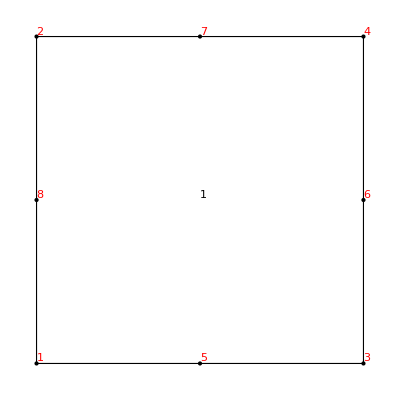
```mathematica
(*-Graphics--Graphics3D-*)
Q1EdgePair[{i1_,i2_,i3_,i4_}]:={{i1,i2},{i2,i3},{i3,i4},{i4,i1}};
H1EdgePair[{i1_,i2_,i3_,i4_,i5_,i6_,i7_,i8_}]:={{i1,i2},{i2,i3},{i3,i4},{i4,i1},{i5,i6},{i6,i7},{i7,i8},{i8,i5},{i1,i5},{i2,i6},{i3,i7},{i4,i8}};
Q1EdgePairS[{i1_,i2_,i3_,i4_}]:={Sort[{i1,i2}],Sort[{i2,i3}],Sort[{i3,i4}],Sort[{i4,i1}]};
H1EdgePairS[{i1_,i2_,i3_,i4_,i5_,i6_,i7_,i8_}]:={Sort[{i1,i2}],Sort[{i2,i3}],Sort[{i3,i4}],Sort[{i4,i1}],Sort[{i5,i6}],Sort[{i6,i7}],Sort[{i7,i8}],Sort[{i8,i5}],Sort[{i1,i5}],Sort[{i2,i6}],Sort[{i3,i7}],Sort[{i4,i8}]};
Q1H1ToQ2H2[ele_List,coord_]:=Block[{ndim=Length[coord[[1]]],len,ep,ep0,asoci,singleK,newCoord,newEle},
If[(Length[ele[[1]]]≠2^ndim),Print["Error, only first order Q1 or H1 element is supported!"];Abort[]];
If[ndim==2,ep=Table[Q1EdgePairS[i],{i,ele}],ep=Table[H1EdgePairS[i],{i,ele}]];
ep=Flatten[ep,1];
ep0=DeleteDuplicates[ep];
asoci=AssociationThread[ep0,Range[Length[ep0]]];
newCoord=Table[0.5(coord[[i[[1]]]]+coord[[i[[2]]]]),{i,ep0}];
(*Print[ep0,ListPlot[coord],ListPlot[newCoord]];*)
singleK=Lookup[asoci,ep,0]+Length[coord];
singleK=ArrayReshape[singleK,{Length[ele],Length[singleK]/Length[ele]}];
newEle=ArrayPad[ele,{{0},{0,If[ndim==2,4,12]}}];
(*Print[Dimensions[newEle],Dimensions[singleK]];*)
newEle[[All,Length[ele[[1]]]+1;;-1]]=singleK;
{newEle,Join[coord,newCoord]}
];
(*Test*)
(*
rg=Cuboid[{0,0,0},{2,1,1}];{m1,coord,ele,eleB,eleP}=Region2Mesh[rg,1];
{cN,eN}=MeshLayerGrow[ele,coord,eleB,eleP,{1,2,5,6},2,0.1];
ShowMesh[m1,True]
ShowMesh[Abaqus2Mesh[cN,eN],True]
ele
eN
{ele2,cN2}=Q1H1ToQ2H2[eN,cN];
ShowMesh[Abaqus2Mesh[cN2,ele2],True]
*)
```

## Plot stream or vector

```mathematica
PlotVectorField[xyz_,vec_]:=ListVectorPlot[Table[{xyz[[i]],vec[[i]]},{i,Length[vec]}](*,VectorPoints->All*)]
PlotTensorField[xyz_,tensor_]:=Block[{vec},vec=TensorAxis2D[tensor];{PlotVectorField[xyz,vec[[All,1;;2]]],PlotVectorField[xyz,vec[[All,3;;4]]]}];
TensorAxis2D=Compile[{{m,_Real,1}(*m11,m12,m22*)},Block[{em,el,ev,a$,b$,c$,em0},{a$,b$,c$}=Chop[m];em=Sqrt[a$^2+4 b$^2-2 a$ c$+c$^2];
em0=If[em<10^-14,10^-14,em];el={0.5 (a$+c$-em0),0.5 (a$+c$+em0)};ev={a$-c$-em+10.^-30,2 b$} /Sqrt[10.^-60+4 b$^2+(a$-c$-em)^2];
If[ev[[1]]<0,ev*=-1];{el[[1]]ev[[1]],el[[1]]ev[[2]],-el[[2]]ev[[2]],el[[2]]ev[[1]]}],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
PlotVectorField[xyz_,vec_,range_]:=ListVectorPlot[Table[{xyz[[i]],vec[[i]]},{i,Length[vec]}](*,VectorPoints->All*),PlotRange->range,VectorPoints->All]
PlotTensorField[xyz_,tensor_,range_]:=Block[{vec},vec=TensorAxis2D[tensor];{PlotVectorField[xyz,vec[[All,1;;2]],PlotRange->range],PlotVectorField[xyz,vec[[All,3;;4]],PlotRange->range]}];

MyStreamPlot0[xVel_,yVel_,mesh_]:=Block[{x,y,xfun,yfun},xfun=ElementMeshInterpolation[{mesh},xVel];yfun=ElementMeshInterpolation[{mesh},yVel];StreamPlot[{xfun[x,y],yfun[x,y]},{x,y}∈mesh,Sequence[AspectRatio->Automatic,PlotRange->All,StreamStyle->Orange,StreamScale->True,PlotLegends->Automatic]]];
(*AbsoluteTiming[uxfun=ElementMeshInterpolation[{m1},uvwN[[All,1]]];]*)
```

```mathematica
PlotTensorField[xyz_,tensor_,mesh_]:=Block[{vec},vec=TensorAxis2D[tensor];{MyStreamPlot0[vec[[All,1]],vec[[All,2]],mesh],MyStreamPlot0[vec[[All,3]],vec[[All,4]],mesh]}];
PlotVectorField[xyz_,vec_,mesh_]:=MyStreamPlot0[vec[[All,1]],vec[[All,2]],mesh]
MyVectorPlot0[xVel_,yVel_,mesh_]:=Block[{x,y,xfun,yfun},xfun=ElementMeshInterpolation[{mesh},xVel];yfun=ElementMeshInterpolation[{mesh},yVel];VectorPlot[{xfun[x,y],yfun[x,y]},{x,y}∈mesh,Sequence[AspectRatio->Automatic,PlotRange->All,VectorScaling->True,PlotLegends->Automatic]]];
MyVectorPlot0[vec_,mesh_]:=Block[{x,y,xfun,yfun},xfun=ElementMeshInterpolation[{mesh},vec[[All,1]]];yfun=ElementMeshInterpolation[{mesh},vec[[All,2]]];VectorPlot[{xfun[x,y],yfun[x,y]},{x,y}∈mesh,Sequence[AspectRatio->Automatic,PlotRange->All,VectorScaling->True,PlotLegends->Automatic]]];
(*AbsoluteTiming[uxfun=ElementMeshInterpolation[{m1},uvwN[[All,1]]];]*)(*very fast.*)
```

```mathematica
(*pts=RandomReal[1,{1000,2}];nF=Nearest[pts->"Index"];
ListPlot[pts,ImageSize->Small,Epilog->(Tooltip[Point[{#}],nF[#][[1]]]&/@pts)]*)
```

```mathematica
MyPlot0[xVel_,yVel_,mesh_,plotFun_:StreamPlot]:=Block[{x,y,xfun,yfun},xfun=ElementMeshInterpolation[{mesh},xVel];yfun=ElementMeshInterpolation[{mesh},yVel];plotFun[{xfun[x,y],yfun[x,y]},{x,y}∈mesh,Sequence[AspectRatio->Automatic,PlotRange->All,StreamStyle->Orange,StreamScale->True,PlotLegends->Automatic]]];
```

### Plot damage field partially.

```mathematica
Clear[DamageVaribleField];
DamageVaribleField[Hdirect_,ele_,coord_,mat0_]:=Block[{HnodeValue},HnodeValue=MeanGaussPointToNode[Hdirect,ele,coord];
If[Depth[mat0]==2,
HnodeValue/(HnodeValue+mat0[[4]]/mat0[[5]]),HnodeValue/(HnodeValue+mat0[[1,4]]/mat0[[1,5]])]];
Clear[DamageVaribleFieldOrder];
DamageVaribleFieldOrder[Hdirect_,ele_,coord_,mat0_]:=Block[{HnodeValue},HnodeValue=MeanGaussPointToNode[Hdirect,ele,coord];
If[Depth[mat0]==2,
HnodeValue/(HnodeValue+mat0[[4]]/mat0[[5]]),HnodeValue/(HnodeValue+mat0[[1,4]]/mat0[[1,5]])]];



FindPointsIndex1D=Compile[{{v1,_Real,1},{xmin,_Real},{xmax,_Real}},Block[{y,r,vt=Table[0,{Length[v1]}]},Do[If[v1[[i]]>xmin&&v1[[i]]<xmax,vt[[i]]=1];,{i,Length[v1]}];
Position[vt,1]]];
SelectData[coord_,nodeValue_,xmin_,xmax_]:=Block[{set1},set1=Flatten[FindPointsIndex1D[nodeValue,xmin,xmax]];{coord[[set1]],nodeValue[[set1]]}];
My3DpointPlot2[coord_,f_]:=Block[{ri=Min[f],rx=Max[f],data},data=Transpose[{coord[[All,1]],coord[[All,2]],coord[[All,3]],f}];
Graphics3D[{({Blend[{Blue,Red},Rescale[Last[#1],{ri,rx}]],Point[Most[#1]]}&)/@data},Boxed->False]];
My3DpointPlot2[coord_,f_,box1_]:=Block[{ri=Min[f],rx=Max[f],data},data=Transpose[{coord[[All,1]],coord[[All,2]],coord[[All,3]],f}];
Graphics3D[{Opacity[0.1],Cuboid[box1[[1]],box1[[2]]],({Blend[{Blue,Red},Rescale[Last[#1],{ri,rx}]],Point[Most[#1]]}&)/@data},Boxed->False]];
PlotDamageField[Hdirect_,ele_,coord_,mat0_,{xmin_,xmax_},box1_]:=Block[{dvalue,cd2,dv2},dvalue=DamageVaribleField[Hdirect,ele,coord,mat0];
{cd2,dv2}=SelectData[coord,dvalue,xmin,xmax];
My3DpointPlot2[cd2,dv2,box1]]
PlotDamageField0[Hdirect_,ele_,coord_,mat0_,{xmin_,xmax_}]:=Block[{dvalue,cd2,dv2},dvalue=DamageVaribleField[Hdirect,ele,coord,mat0];
{cd2,dv2}=SelectData[coord,dvalue,xmin,xmax];
My3DpointPlot2[cd2,dv2]]
```

```mathematica
Clear[DamageVaribleFieldOrder];
DamageVaribleFieldOrder[Hdirect_,ele_,coord_,mat0_]:=Block[{HnodeValue,gc,lp,vdT},
HnodeValue=MeanGaussPointToNode[Hdirect,ele,coord];
If[Depth[mat0]==2,gc=mat0[[4]];lp=mat0[[5]];vdT=mat0[[7]],gc=mat0[[1,4]];lp=mat0[[1,5]];vdT=mat0[[1,7]]];
DamageValueSRCompile[HnodeValue,lp,gc,vdT]
];
DamageValueSRCompile=Compile[{{HmaxI,_Real},{lp,_Real},{gc,_Real},{vdT,_Real}},Block[{sValue,(*rValue,*)tempValue},
tempValue=HmaxI lp/gc (1+Abs[vdT]);
If[vdT<0,(*(damage model without treshold value)*) 
sValue=Power[(lp HmaxI/gc),-1/vdT]/(1+Power[lp HmaxI/gc,-1/vdT]);
(*rValue=1/Power[1+Power[lp HmaxI/gc,-1/vdT],1-vdT];*),
(*(damage model with treshold value)*) 
sValue=If[tempValue<=1.,0.,1-Power[tempValue,-1/vdT]];
(*rValue=If[tempValue<=1.,1.,Power[tempValue,-(vdT+1)/vdT]];*)];
sValue],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False,"ExpressionOptimization"->True},RuntimeAttributes->{Listable},Parallelization->True];
(*DateObject[{2023,10,25},"Day"]*)
```

## Q1 H1 mesh refinement. 1:3.

#### There are several cases should be considered. In 2D,

-Graphics-2D.
3D: -Graphics--Graphics-
   -Graphics--Graphics-
   Q1 counter-clockwise. H1 clockwise
Q1 Permutation: {1,2,3,4}, {2,3,4,1},{3,4,1,2},{4,1,2,3}.
H1 Permutation:  {1,2,3,4,5,6,7,8}, {1,5,6,2,4,8,7,3},{2,6,7,3,1,5,8,4},{1,4,8,5,2,3,7,6},{5,8,7,6,1,4,3,2},{3,7,8,4,2,6,5,1};

Q1 BC: {{1,2},{2,3},{3,4},{4,1}}
H1 BC: {{1,2,3,4},{5,6,7,8}, {1,5,6,2},{4,8,7,3},{2,6,7,3},{1,5,8,4}}

```mathematica
(*MathematicaQ1H1TOAbaqus[ele_]:=If[Length[ele[[1]]]==4,ele,ele[[All,]]]*)
```

```mathematica
Clear[Mesh2Abaqus];
Mesh2Abaqus[file_,coord_,ele_]:=Block[{len,elen,strAll,scoord,sele,ci,
shead="*Heading\nMesh from Mathematica\n*Part, name=part1\n*Node\n",
selement,send="*End Part"},elen=Length[ele[[1]]];
If[FileExistsQ[file],Print["Warning, existed file was deleted!"];DeleteFile[file]];
If[Length[coord[[1]]]==2,selement=If[elen==4,"*Element, type=CPS4\n***CPS4 for plane stress, CPE4 for plane strain\n","*Element, type=CPS3\n***CPS3 for plane stress, CPE3 for plane strain\n"],selement=If[elen==8,"*Element, type=C3D8\n","*Element, type=C3D4\n"]];
scoord=Table[ci=StringJoin[Riffle[Prepend[DoubleToString[coord[[i]]],"  "<>ToString[i]],", "]]<>"\n",{i,Length[coord]}];
sele=Table[ci=StringJoin[Riffle[Prepend[IntegerToString[ele[[i]]],"  "<>ToString[i]],", "]]<>"\n",{i,Length[ele]}];
strAll=shead<>StringJoin[scoord]<>selement<>StringJoin[sele]<>send;
Export[file<>".txt",strAll];
RenameFile[file<>".txt",file];file
]
(*Mesh2AbaqusInput[NotebookDirectory[]<>"testinp4.inp",coord,ele](*worked. LS prepost crashed.*)*)
DoubleToString[a_]:=StringReplace[Internal`MRealToString[N[a]],{"*^"->"e","`"->""}]
SetAttributes[DoubleToString,Listable]
IntegerToString[a_]:=ToString[a];
SetAttributes[IntegerToString,Listable]
(*
*)
```

```mathematica
H1permutation[e8_List]:=Block[{face,pair,facePer},If[Length[e8]!=8,Abort[]];face={{1,2,3,4,5,6,7,8},{1,5,6,2,4,8,7,3},{2,6,7,3,1,5,8,4},{1,4,8,5,2,3,7,6},{5,8,7,6,1,4,3,2},{3,7,8,4,2,6,5,1}};
facePer={{1,2,3,4},{2,3,4,1},{3,4,1,2},{4,1,2,3}};
pair=Flatten[Table[Table[Join[face[[i,ii]],face[[i,ii+4]]],{ii,facePer}],{i,6}],1];
Table[e8[[i]],{i,pair}]
]
(*(*Test: there are 24 forms of node list to represent an H1 element.*)
rg=Cuboid[{0,0,0},{1,1,1}];{m1,coord,ele,eleB,eleP}=Region2Mesh[rg,1];ele
ShowMesh[m1,True]
ep=H1permutation[ele[[1]]];
Table[ShowMesh[Abaqus2Mesh[coord,{ei}],True],{ei,ep}]
*)
```

## Mesh coord reordering RCM

```mathematica
Needs["GraphUtilities`"]
Mesh2ListOrdered=Compile[{{ei,_Integer,1},{nShift,_Integer}},Block[{e2=Sort[ei],eL,k=1,len=Length[ei]},eL=Table[0,{IntegerPart[len(len-1)/2]}];
Do[Do[eL[[k++]]=e2[[i]] nShift+e2[[j]],{j,i+1,len}],{i,len}];eL
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True];
Mesh2ListOrderedNo=Compile[{{ei,_Integer,1},{nShift,_Integer}},Block[{e2=ei,eL,k=1,len=Length[ei]},eL=Table[0,{len(len-1)}];(*Print[eL];*)
Do[Do[eL[[k++]]=e2[[i]] nShift+e2[[j]];eL[[k++]]=e2[[j]] nShift+e2[[i]];,{j,i+1,len}],{i,len}];eL
],CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},(*CompilationTarget->"C",*)RuntimeAttributes->{Listable},Parallelization->True];

MeshMinimumBandwidthOrdering[meshList_]:=Block[{nMax=Max[meshList],mgraph,ej,nshift,res},nshift=10^IntegerPart[Ceiling[Log10[nMax]]];
mgraph=DeleteDuplicates[Flatten[Mesh2ListOrderedNo[meshList,nshift],1]];
mgraph=QuotientRemainder[mgraph,nshift];
mgraph=SparseArray[Thread[mgraph->1],{nMax,nMax}];
res=MinimumBandwidthOrdering[mgraph][[1]];(*];*)res
]

FEMMeshReordering[coord_,meshList_]:=Block[{gh,m2},(*xt1=AbsoluteTiming[*)gh=MeshMinimumBandwidthOrdering[meshList];m2=meshList/.Dispatch[Thread[gh->Range[Length[gh]]]];(*];*)(*xgh=gh;*)
{coord[[gh]],m2}
]
(*90k H1, takes 25s to index-reordering, MinimumBandwidthOrdering is very slow. {{23.106532,Null},{24.9946448,Null},{0.2601026,Null}}

Use symmetric sparse matrix, the time is reduced from 25 to 4 seconds. Sparse matrix is much faster than Graph in the function of MinimumBandwidthOrdering
 *)
(*Test RCM performance*)
(*n=2000000;a=SparseArray[{Band[{1,1}]->Random[],Band[{1,2}]->Random[],Band[{2,1}]->Random[]},{n,n}];
a+=aᵀ;p=Ordering[RandomReal[1,{n}]];
(*q=Ordering[RandomReal[1,{n}]];*)
b=a[[p,p]];
a=N[a];b=N[b];xp=N[p];
x1=LinearSolve[a,xp,Method->"Pardiso"];//AbsoluteTiming
x2=LinearSolve[b,xp[[p]],Method->"Pardiso"];//AbsoluteTiming
Norm[x1[[p]]-x2]/Norm[x2]*)
(*{{2.7941252,Null},{5.6025204,Null},8.226559044813807*^-14}*)
(*RCM can save half time for 2 million dofs.*)
```